This file outlines the code utilized to make figures and perform analysis in the paper “Response to Comment on ‘Innovative scattering analysis shows that hydrophobic disordered proteins are expanded in water’ ”

Please note that to avoid any copyright issues we have NOT uploaded data used from previous papers PDFs which were not provided to us. Email trsosnic@uchicago.edu or jriback@uchicago.edu for more details.

# Code To Load

This includes both code developed for this paper and previous code reported and developed in “Innovative scattering analysis shows hydrophobic disordered proteins are expanded in water” (Riback et al., 2017 Science).

### General commands

```mathematica
MASTERDIRECTORY="/Users/josh/Desktop/manuscrips/PNt_Paper/github/SAXSonIDPs/";
If[DirectoryQ[MASTERDIRECTORY]==False,CreateDirectory[MASTERDIRECTORY]];
SetDirectory[MASTERDIRECTORY];
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
ConvertToErrorBar[DAT_,funcx_:(#&),funcy_:(#&)]:={{funcx[#[[1]]],If[Im[#]≠0,0,#]&@funcy[#[[2]]]},ErrorBar[{If[Im[#]≠0,-100,#]&@(funcy[#[[2]]-#[[3]]]-funcy[#[[2]]]),If[Im[#]≠0,100,#]&@(funcy[#[[2]]+#[[3]]]-funcy[#[[2]]])}]}&/@DAT
```

```mathematica
Colors={GrayLevel[0],RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.471412, 0.108766, 0.527016]}
```

{GrayLevel[0],RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.471412, 0.108766, 0.527016]}

```mathematica
A[z_]:=(*-EulerGamma+CoshIntegral[z]-Log[z]+SinhIntegral[z]*)(*Later found*)-EulerGamma-Gamma[0,-z]-Log[-z]
```

```mathematica
RNSARW[I0_,Rg_]:=(2 ⅇ^(-1/8-((0.8644527786254743 ⅇ^(-1.156801186514841 q^2 Rg^2))/(q^2 Rg^2)-(0.7472786064733034 ⅇ^(-1.156801186514841 q^2 Rg^2) (-EulerGamma-Gamma[0,-1.156801186514841 q^2 Rg^2]-Log[-1.156801186514841 q^2 Rg^2]))/(q^4 Rg^4)+(0.8644527786254743 ⅇ^(-1.156801186514841 q^2 Rg^2) (-EulerGamma-Gamma[0,-1.156801186514841 q^2 Rg^2]-Log[-1.156801186514841 q^2 Rg^2]))/(q^2 Rg^2)+2 NIntegrate[(Exp[-(1.156801186514841 q^2 Rg^2)] A[1.156801186514841 q^2 Rg^2-(1.156801186514841 q^2 Rg^2) t (1-t)])/((1.156801186514841 q^2 Rg^2)^2)+(1/(1.156801186514841 q^2 Rg^2)-1/((1.156801186514841 q^2 Rg^2)^2)) A[-(1.156801186514841 q^2 Rg^2) t (1-t)]-(1-Exp[-(1.156801186514841 q^2 Rg^2) t (1-t)])/((1.156801186514841 q^2 Rg^2)^2 t (1-t)),{t,0,1},Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->5]+NIntegrate[1/((1.156801186514841 q^2 Rg^2) (1-t))+(Exp[-(1.156801186514841 q^2 Rg^2) t (1-t)]-1)/((1.156801186514841 q^2 Rg^2)^2 t (1-t)^2),{t,0,1},Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->5])/(8 (-0.7472786064733034/(q^4 Rg^4)+(0.7472786064733034 ⅇ^(-1.156801186514841 q^2 Rg^2))/(q^4 Rg^4)+0.8644527786254743/(q^2 Rg^2)))) Abs[I0] (-0.7472786064733034/(q^4 Rg^4)+(0.7472786064733034 ⅇ^(-1.156801186514841 q^2 Rg^2))/(q^4 Rg^4)+0.8644527786254743/(q^2 Rg^2)))/.{q->#}&;
```

```mathematica
Gunier[I0_,Rg_]:=(Abs[I0]*Exp[-q^2 Rg^2/3])/.{q->#}&;
```

```mathematica
Debye[I0_,Rg_]:=(I0(2(Exp[-q^2 Rg^2]-1+q^2 Rg^2))/((q^2 Rg^2)^2))/.{q->#}&;
```

```mathematica
SGC[I0_,Rg_,ν_]:=(2I0 NIntegrate[(1-zz)Exp[- q^2 Rg^2/6(1+2Abs[ν])(2+2Abs[ν])zz^(2Abs[ν])],{zz,0,1},Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->5])/.{q->#}&;
```

```mathematica
Module[{interp=Interpolation[Table[{x,Re[RNSARW[1,1][x]]},{x,0.015,20.,0.025}]]},RNSARWINTERP[I0_,Rg_]:=(I0*interp[q*Rg])/.{q->#}&];
```

NIntegrate::inumr: The integrand -(0.747279 (1-ⅇ^(-1.1568 q^2 (1+Times[«2»]) t)))/(q^4 (1-t) t)+(-0.747279/q^4+0.864453/q^2) (-EulerGamma-Gamma[0,1.1568 q^2 (1+Times[«2»]) t]-Log[1.1568 q^2 (1+Times[«2»]) t])+(0.747279 ⅇ^(«1») (-EulerGamma-Gamma[0,-1.1568 Power[«2»]+«18» «3»]-Log[-1.1568 Power[«2»]+1.1568 Power[«2»] Plus[«2»] t]))/q^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand 0.864453/(q^2 (1-t))+(0.747279 (-1+ⅇ^(-1.1568 q^2 (1-t) t)))/(q^4 (1-t)^2 t) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand -(0.747279 (1-ⅇ^(-1.1568 q^2 (1+Times[«2»]) t)))/(q^4 (1-t) t)+(-0.747279/q^4+0.864453/q^2) (-EulerGamma-Gamma[0,1.1568 q^2 (1+Times[«2»]) t]-Log[1.1568 q^2 (1+Times[«2»]) t])+(0.747279 ⅇ^(«1») (-EulerGamma-Gamma[0,-1.1568 Power[«2»]+«18» «3»]-Log[-1.1568 Power[«2»]+1.1568 Power[«2»] Plus[«2»] t]))/q^4 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

### Rij Code

```mathematica
Clear[IMPORTRij]
IMPORTRij[name_]:=IMPORTRij[name]=Import["SimulationData/"<>name<>"_Rij","Text"]
```

```mathematica
Clear[SCALEFITSRij];SCALEFITSRij[name_,start_:1,end_:-1]:=Module[{datas=Select[ToExpression[StringSplit[#," "]]&/@StringSplit[#,"\n"][[2;;]],15<#[[1]]&]&/@StringSplit[IMPORTRij[name],"\n\n"],fits},fits=Evaluate[NonlinearModelFit[#[[start;;end,;;2]],R0 n^ν,{{R0,6},{ν,0.52}},n,Weights->((#[[3]])^-2&/@#[[start;;end]]),MaxIterations->Infinity,Method->"LevenbergMarquardt"]&/@datas ];(#["ParameterTable"][[1,1,2;;,{2,3}]])&/@fits]
```

### SAXS Code

```mathematica
Clear[IqDat]
IqDat[daz_]:=Module[{first={ToExpression@Transpose[{0.005*(Range[Length[StringSplit[#[[1]]]]]-1),StringSplit[#[[1]]]}],#[[2]]}&/@daz,second,qRgs,third},second={#[[1]],{Mean[#[[2]]],StandardDeviation[#[[2]]]/Sqrt[Length[#[[2]]]]}}&@Transpose[({Transpose[{#[[1,;;,1]]*#[[2]],(#[[1,;;,2]])/1000.}],#[[2]]}&/@first)];({IqDat[daz,qRg_]:={Mean[#],StandardDeviation[#]/Sqrt[Length[#]]}&@(Interpolation[#,qRg]&/@second[[1]]),IqDat[daz]=second[[2]]}[[2]])]
IqDat[daz_,NADA_]:=Module[{first={ToExpression@Transpose[{0.005*(Range[Length[StringSplit[#[[1]]]]]-1),StringSplit[#[[1]]]}],#[[2]]}&/@daz,second,qRgs,third},second={#[[1]],{Mean[#[[2]]],StandardDeviation[#[[2]]]/Sqrt[Length[#[[2]]]]}}&@Transpose[({Transpose[{#[[1,;;,1]]*#[[2]],(#[[1,;;,2]])/1000.}],#[[2]]}&/@first)];({IqDat[daz,qRg_]:={Mean[#],StandardDeviation[#]/Sqrt[Length[#]]}&@(Interpolation[#,qRg]&/@second[[1]]),{Mean[#],StandardDeviation[#]/Sqrt[Length[#]]}&@(Interpolation[#,NADA]&/@second[[1]])}[[2]])]
```

```mathematica
Clear[IqDats,IqDatsqRg]
IqDats[name_]:=IqDat/@IMPORTSAXS[name]
IqDatsqRg[name_]:=(IqDat[#,qRg]&/@IMPORTSAXS[name])/.{qRg->#}&
```

```mathematica
Clear[IMPORTSAXS]
IMPORTSAXS[name_,partial_:""]:=({IMPORTSAXS[name]=ToExpression[StringReplace[Import["SimulationData/"<>name<>"_SCATTERING"<>partial<>"FOXSall","Text"],{"\n"->" "}]<>"}"],IqDats[name]};"LOAD "<>name<>" complete")
```

### MFF Code

#### CODE (figures, interpolation, and fitting)

```mathematica
Clear[TWOERRORFUNC];
TWOERRORFUNC[first_,second_]:={{#[[1,1]],#[[2,1]]},ErrorBar[#[[1,2]],#[[2,2]]]}&/@Transpose[{first,second}];
```

```mathematica
avLOGLOG[pnts_,f1_,f2_,i_]:=(({{Mean[#1⟦1⟧],Mean[#1⟦2⟧]},ErrorBar[(√Total[(#1⟦3⟧)^2])/Length[#1⟦2⟧]]}&)[Transpose[#1]]&)/@Split[({f1@@#1,f2@@#1,Abs[Derivative[0,1][f2]@@#1] (#3&)@@#1}&)/@pnts,Round[i Log10[#1⟦1⟧]]==Round[i Log10[#2⟦1⟧]]&]
```

```mathematica
MakeDataPrettySARWF2[fileid_,i_,FIT_:SARWFit,f1_:(#1&),f2_:(#2/A1&),δx_:0,δy_:0]:=Block[{fit=FIT[fileid],A1,RG,file,startfit,endfit,av},A1=I0/.fit⟦-1⟧["BestFitParameters"];RG=Rg/.fit⟦-1⟧["BestFitParameters"];av[pnts_]:=(({{Mean[#1⟦1⟧],Mean[#1⟦2⟧]},ErrorBar[(√Total[(#1⟦3⟧)^2])/Length[#1⟦2⟧]]}&)[Transpose[#1]]&)/@Split[({f1@@#1,f2@@#1,Abs[Derivative[0,1][f2]@@#1] (#3&)@@#1}&)/@pnts,Round[i Log10[#1⟦1⟧]]==Round[i Log10[#2⟦1⟧]]&];av[Flatten[fit[[;;-2]],1]]]
```

```mathematica
Clear[MakeDataPrettyLogLog2]
MakeDataPrettyLogLog2[fileid_,i_,FIT_:DebyeFit,f1_:(Log10[#1]&),f2_:(Log10[#1/A1]&),δx_:0,δy_:0]:=Block[{fit=FIT[fileid],A1,RG,file,startfit,endfit,av},A1=Abs[I0]/.fit⟦-1⟧["BestFitParameters"];RG=Rg/.fit⟦-1⟧["BestFitParameters"];av[pnts_]:=(({{f1[#1⟦1⟧],f2[#1⟦2⟧]},ErrorBar[{Log10[(If[#1<0,1/10^4,#1]&)[1-(#1⟦3⟧)/(#1⟦2⟧)]],Log10[1+(#1⟦3⟧)/(#1⟦2⟧)]}]}&)[({Mean[#1⟦1⟧],Mean[#1⟦2⟧],(√Total[(#1⟦3⟧)^2])/Length[#1⟦2⟧]}&)[Transpose[#1]]]&)/@Split[({#1⟦1⟧,#1⟦2⟧,#1⟦3⟧}&)/@pnts,Round[i Log10[#1⟦1⟧]]==Round[i Log10[#2⟦1⟧]]&];av[fit[[1]]]]
```

```mathematica
Clear[FITGENERALi]
FITGENERALi[name_]:=(FITGENERALi[name]=FITGENERAL[name]/.{ν->#1,q->#2}&)
```

```mathematica
Clear[FITGENERAL];
FITGENERAL[SAXSDATA_,RGDATA_,NAME_]:=FITGENERAL[SAXSDATA,RGDATA,NAME]=FITGENERAL[NAME]=(Print["STARTING FIT"];Module[{first=Transpose[Table[If[4Round[(x-0.001)/4]==(x-0.001),Print[x]];Module[{data=Transpose[{RGDATA,SAXSDATA[x]}],fit,fitl,fith,minmax},
minmax={#[[1]]-0.01,#[[2]]+0.01}&@MinMax[data[[;;,1,1]]];fit=LinearModelFit[data[[;;,;;,1]],Table[BernsteinBasis[3,i,(z-minmax[[1]])/(minmax[[2]]-minmax[[1]])],{i,0,3}],z,IncludeConstantBasis->False];{x,#}&/@fit["BestFitParameters"](*{{x,param0},{x,param1},{x,param2},{x,param3},{x,param4}}*)],{x,0.001,20,0.5}]],QuadraticInterpolation,QUADINTERPν,minmax},
minmax={#[[1]]-0.01,#[[2]]+0.01}&@MinMax[RGDATA[[;;,1]]];
QuadraticInterpolation;QUADINTERPν={(Sum[Interpolation[#[[i+1]],q]BernsteinBasis[3,i,(ν-minmax[[1]])/(minmax[[2]]-minmax[[1]])],{i,0,3}])&@first};QUADINTERPν(*/.{q->#[[2]],ν->#[[1]]}*)])
```

```mathematica
avgroup[pnts_,f1_,f2_,i_]:=(({Mean[#1⟦1⟧],Mean[#1⟦2⟧],(√Total[(#1⟦3⟧)^2])/Length[#1⟦2⟧]}&)[Transpose[#1]]&)/@Split[({f1@@#1,f2@@#1,Abs[Derivative[0,1][f2]@@#1] (#3&)@@#1}&)/@pnts,Round[i Log10[#1⟦1⟧]]==Round[i Log10[#2⟦1⟧]](*Round[i #1⟦1⟧]==Round[i #2⟦1⟧]*)&]
```

```mathematica
Clear[χ2func]
χ2func[func_,dat_,min_,max_,num_:20]:=χ2func[func,dat,min,max]=Mean[((I0 func[ν,#[[1]]Rg][[1]]-#[[2]])/(#[[3]](*(I0 func[ν,#[[1]]Rg][[2]])^2*)))^2&/@avgroup[Select[Import[StringDrop[dat,-4]<>".dat","Table"],min<#[[1]]<max&],#1&,#2&,num]]
```

```mathematica
Clear[ROUNDSEARCH]
ROUNDSEARCH[Prev_,func_,dat_,min_,max_]:=Module[{χ2=χ2func[func,dat,min,max],NEXTSEARCH,RESULTNEXTSEARCH,rank,result},NEXTSEARCH=Partition[Flatten[Table[{I0,Rg,ν},{I0,Prev[[1,1]],Prev[[1,2]],(Prev[[1,2]]-Prev[[1,1]])/10},{Rg,Prev[[2,1]],Prev[[2,2]],(Prev[[2,2]]-Prev[[2,1]])/10},{ν,Prev[[3,1]],Prev[[3,2]],(Prev[[3,2]]-Prev[[3,1]])/10}]],3];RESULTNEXTSEARCH=(χ2/.{I0->#[[1]],Rg->#[[2]],ν->#[[3]]})&/@NEXTSEARCH;rank=RankedMax[Exp[-RESULTNEXTSEARCH]/Total[Exp[-RESULTNEXTSEARCH]],50];(*Print[rank];*)result=(Transpose@NEXTSEARCH[[Position[Exp[-RESULTNEXTSEARCH]/Total[Exp[-RESULTNEXTSEARCH]],a_/;a>rank][[;;,1]]]]);(*Print[{Mean[#],StandardDeviation[#]}&/@result]*){Mean[#]-StandardDeviation[#],Mean[#]+StandardDeviation[#]}&/@result]
```

```mathematica
Clear[FITZ]
FITZ[FUNC_,file_,parami_,min_,max_]:=FITZ[FUNC,file,min,max]=Module[{first=(Mean/@Nest[ROUNDSEARCH[#,FUNC,file,min,max]&,parami(*{{1000.Log[2],1000./Log[2]},{40.,70},{0.4,0.62}}*),2]),second,third,fit,dat},Print[first];
dat=Select[Import[StringDrop[file,-4]<>".dat","Table"],min<#[[1]]<max&];
fit=
NonlinearModelFit[dat[[;;,;;2]],Evaluate[Abs[I0]*FUNC[Abs[ν],Abs[Rg]q][[1]]](*0.4<ν<0.61}*),{{I0,first[[1]]},{ν,first[[3]]},{Rg,first[[2]]}},q,Weights->(1/(#[[3]])^2&/@dat),MaxIterations->Infinity];Print[{fit["ParameterTable"](*χ2func[FUNC,file,min,max]/.fit["BestFitParameters"]*)}];{Import[StringDrop[file,-4]<>".dat","Table"],dat,fit}]
```

```mathematica
Clear[FITSAXSPROFILE];
FITSAXSPROFILE[name_,func_,rgmin_,rgmax_,qmin_,qmax_]:=FITSAXSPROFILE[name,func,rgmin,rgmax,qmin,qmax]=FITSAXSPROFILE[name,func]=Module[{val=Mean[Select[Import[name,"Table"],0.01<#[[1]]<0.015&][[;;,2]]]},FITZ[func,name,{{val Log[2.],val/Log[2.]},N[{rgmin,rgmax}],{0.4,0.61}},qmin,qmax]]
```

```mathematica
Clear[CreateMFF]
CreateMFF[name_,partial_:""]:=(Print[IMPORTSAXS[name,partial]];FITGENERAL[IqDatsqRg[name],SCALEFITSRij[name][[;;,2]],name];"DONE MAKING MFF")
```

### Rg vs ν

```mathematica
Clear[fitνandRg];fitνandRg[name_]:=fitνandRg[name]=LinearModelFit[Transpose[{{#[[1]],#[[2]]}&/@SCALEFITSRij[name][[;;,2]],IqDats[name]}][[;;,;;,1]],{xx,xx^2,xx^3},xx,Weights->(((#[[1]])^-2(*(#[[2]])^-2*))&/@Transpose[{{#[[1]],#[[2]]}&/@SCALEFITSRij[name][[;;,2]],IqDats[name]}][[;;,;;,2]])]
```

```mathematica
Clear[dataνandRg];dataνandRg[name_]:=dataνandRg[name]=TWOERRORFUNC[{#[[1]],#[[2]]}&/@Flatten[{(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,maxq][[-1]]["ParameterTable"][[1,1,3,{2,3}]]&/@FILESPNt[[2;;-3]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,0.1][[-1]]["ParameterTable"][[1,1,3,{2,3}]]&/@FILESPNt[[{-2}]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,0.075][[-1]]["ParameterTable"][[1,1,3,{2,3}]]&/@FILESPNt[[{-1}]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,maxq][[-1]]["ParameterTable"][[1,1,3,{2,3}]]&/@FILESPNt[[{1}]])},1],Flatten[{(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,maxq][[-1]]["ParameterTable"][[1,1,4,{2,3}]]&/@FILESPNt[[2;;-3]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,0.1][[-1]]["ParameterTable"][[1,1,4,{2,3}]]&/@FILESPNt[[{-2}]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,0.075][[-1]]["ParameterTable"][[1,1,4,{2,3}]]&/@FILESPNt[[{-1}]]),(FITSAXSPROFILE[#,NEWFUNCFITHOMO,45,65,0.01,maxq][[-1]]["ParameterTable"][[1,1,4,{2,3}]]&/@FILESPNt[[{1}]])},1]];
```

```mathematica
Clear[dataνandRg2];dataνandRg2[name_]:=dataνandRg2[name]=TWOERRORFUNC[{#[[1]],#[[2]]}&/@(FITSAXSPROFILE[#,FITGENERALi[name],25,45,0.01,maxq][[-1]]["ParameterTable"][[1,1,3,{2,3}]]&/@FILESOther),(FITSAXSPROFILE[#,FITGENERALi[name],25,45,0.01,maxq][[-1]]["ParameterTable"][[1,1,4,{2,3}]]&/@FILESOther)]
```

# Load Data

See figure code below for relevant citations when applicable.

## Parse FRET-Reweight model data (For Fig. 1)

Data used in this figure are from. “Consistent View of Polypeptide Chain Expansion in Chemical Denaturants from Multiple Experimental Methods.” (Borgia et al., 2016 JACS).

Please download supplement to process this data. To avoid any copyright issues we have NOT uploaded this file.

```mathematica
ParseFRETreW=Import[NotebookDirectory[]<>"/Data/BorgiaSupp.pdf",{"Pages",29}];
```

R17 Gdn

```mathematica
R17GdnFRETReWxy=ParseFRETreW[[1,1,69,1,1,2,1]];
```

```mathematica
ParseFRETreW[[1,1,{89,92},1,1,2,1,1,1]]
{a,b}/.NSolve[{a*%[[1]]+b==0,a*%[[2]]+b==1},{a,b}][[1]]
R17GdnFRETReWx=(#[[1]]*%[[1]]+%[[2]])&/@R17GdnFRETReWxy
```

{156.36,176.7}

{0.0491642,-7.68732}

{0.581121,1.0767,1.52802,2.0472,2.52802,3.0649,3.9823,4.95575,6.92035}

```mathematica
ParseFRETreW[[1,1,{113,117},1,1,2,1,1,2]]
{a,b}/.NSolve[{a*%[[1]]+b==2.6,a*%[[2]]+b==3.0},{a,b}][[1]]
R17GdnFRETReWy=10(#[[2]]*%[[1]]+%[[2]])&/@R17GdnFRETReWxy
```

{583.46,617.42}

{0.0117786,-4.27232}

{29.7314,32.947,33.4205,35.0318,36.9329,38.2968,39.1449,38.5795,39.9576}

ACTR Gdn

```mathematica
ACTRGdnFRETReWxy=ParseFRETreW[[1,1,230,1,1,2,1]];
```

```mathematica
ParseFRETreW[[1,1,{252,255},1,1,2,1,1,1]]
{a,b}/.NSolve[{a*%[[1]]+b==0,a*%[[2]]+b==1},{a,b}][[1]]
ACTRGdnFRETReWx=(#[[1]]*%[[1]]+%[[2]])&/@ACTRGdnFRETReWxy
```

{343.32,362.34}

{0.0525762,-18.0505}

{0.318612,0.570978,1.03785,1.53943,2.01262,2.50158,3.01577,3.99685,4.9653,6.95268}

```mathematica
ParseFRETreW[[1,1,{276,279},1,1,2,1,1,2]]
{a,b}/.NSolve[{a*%[[1]]+b==2.4,a*%[[2]]+b==2.8},{a,b}][[1]]
ACTRGdnFRETReWy=10(#[[2]]*%[[1]]+%[[2]])&/@ACTRGdnFRETReWxy
```

{597.92,655.46}

{0.00695169,-1.75655}

{24.0834,24.4088,25.2138,25.0719,26.4108,25.9395,26.7195,28.3587,29.0052,29.4223}

R17 Urea

```mathematica
R17UreaFRETReWxy=ParseFRETreW[[1,1,362,1,1,2,1]];
```

```mathematica
ParseFRETreW[[1,1,{384,387},1,1,2,1,1,1]]
{a,b}/.NSolve[{a*%[[1]]+b==0,a*%[[2]]+b==2},{a,b}][[1]]
R17UreaFRETReWx=(#[[1]]*%[[1]]+%[[2]])&/@R17UreaFRETReWxy
```

{156.36,188.52}

{0.0621891,-9.72388}

{0.619403,1.1306,1.60821,2.1194,2.61194,3.10075,4.20896,5.05224,7.03731,8.99254}

```mathematica
ParseFRETreW[[1,1,{399,402},1,1,2,1,1,2]]
{a,b}/.NSolve[{a*%[[1]]+b==2.6,a*%[[2]]+b==3.0},{a,b}][[1]]
R17UreaFRETReWy=10(#[[2]]*%[[1]]+%[[2]])&/@R17UreaFRETReWxy
```

{402.02,435.86}

{0.0118203,-2.15201}

{27.922,29.5887,30.,32.461,31.9645,32.0638,33.844,35.383,37.844,38.9929}

ACTR Urea

```mathematica
ACTRUreaFRETReWxy=ParseFRETreW[[1,1,490,1,1,2,1]];
```

```mathematica
ParseFRETreW[[1,1,{512,515},1,1,2,1,1,1]]
{a,b}/.NSolve[{a*%[[1]]+b==0,a*%[[2]]+b==2},{a,b}][[1]]
ACTRUreaFRETReWx=(#[[1]]*%[[1]]+%[[2]])&/@ACTRUreaFRETReWxy
```

{341.4,371.88}

{0.0656168,-22.4016}

{0.57874,1.09843,1.55118,2.0315,2.52756,3.01181,3.97638,4.9685,6.98425,8.95276}

```mathematica
ParseFRETreW[[1,1,{527,530},1,1,2,1,1,2]]
{a,b}/.NSolve[{a*%[[1]]+b==2.4,a*%[[2]]+b==2.8},{a,b}][[1]]
ACTRUreaFRETReWy=10(#[[2]]*%[[1]]+%[[2]])&/@ACTRUreaFRETReWxy
```

{416.36,473.9}

{0.00695169,-0.494404}

{26.1022,26.3525,25.9771,26.878,26.6778,27.5495,28.7883,27.9082,29.2555,30.5777}

## Parse SAXS-Reweight model data (For Fig. 1)

Data used in this figure are from. “Consistent View of Polypeptide Chain Expansion in Chemical Denaturants from Multiple Experimental Methods.” (Borgia et al., 2016 JACS).

Please download supplement to process this data. To avoid any copyright issues we have NOT uploaded this file.

```mathematica
ParseFRETreW=Import[NotebookDirectory[]<>"/Data/BorgiaSupp.pdf",{"Pages",29}];
```

R17 Gdn

```mathematica
R17GdnSAXSReWxy=ParseFRETreW[[1,1,88,1,1,2,1]];
```

```mathematica
ParseFRETreW[[1,1,{89,92},1,1,2,1,1,1]]
{a,b}/.NSolve[{a*%[[1]]+b==0,a*%[[2]]+b==1},{a,b}][[1]]
R17GdnSAXSReWx=(#[[1]]*%[[1]]+%[[2]])&/@R17GdnSAXSReWxy
```

{156.36,176.7}

{0.0491642,-7.68732}

{0.581121,1.0767,1.52802,2.0472,2.52802,3.0649,3.9823,4.95575,6.92035}

```mathematica
ParseFRETreW[[1,1,{113,117},1,1,2,1,1,2]]
{a,b}/.NSolve[{a*%[[1]]+b==2.6,a*%[[2]]+b==3.0},{a,b}][[1]]
R17GdnSAXSReWy=10(#[[2]]*%[[1]]+%[[2]])&/@R17GdnSAXSReWxy
```

{583.46,617.42}

{0.0117786,-4.27232}

{34.8622,35.689,35.0035,35.8869,38.0565,38.3251,38.2827,39.258,40.2827}

ACTR Gdn

```mathematica
ACTRGdnSAXSReWxy=ParseFRETreW[[1,1,251,1,1,2,1]];
```

```mathematica
ParseFRETreW[[1,1,{252,255},1,1,2,1,1,1]]
{a,b}/.NSolve[{a*%[[1]]+b==0,a*%[[2]]+b==1},{a,b}][[1]]
ACTRGdnSAXSReWx=(#[[1]]*%[[1]]+%[[2]])&/@ACTRGdnSAXSReWxy
```

{343.32,362.34}

{0.0525762,-18.0505}

{0.318612,0.570978,1.03785,1.53943,2.01262,2.50158,3.01577,3.99685,4.9653,6.95268}

```mathematica
ParseFRETreW[[1,1,{276,279},1,1,2,1,1,2]]
{a,b}/.NSolve[{a*%[[1]]+b==2.4,a*%[[2]]+b==2.8},{a,b}][[1]]
ACTRGdnSAXSReWy=10(#[[2]]*%[[1]]+%[[2]])&/@ACTRGdnSAXSReWxy
```

{597.92,655.46}

{0.00695169,-1.75655}

{25.0553,25.3472,26.0188,26.8863,27.4745,28.7466,29.1387,28.,30.194,29.2138}

R17 Urea

```mathematica
R17UreaSAXSReWxy=ParseFRETreW[[1,1,383,1,1,2,1]];
```

```mathematica
ParseFRETreW[[1,1,{384,387},1,1,2,1,1,1]]
{a,b}/.NSolve[{a*%[[1]]+b==0,a*%[[2]]+b==2},{a,b}][[1]]
R17UreaSAXSReWx=(#[[1]]*%[[1]]+%[[2]])&/@R17UreaSAXSReWxy
```

{156.36,188.52}

{0.0621891,-9.72388}

{0.619403,1.1306,1.60821,2.1194,2.61194,3.10075,4.20896,5.05224,7.03731,8.99254}

```mathematica
ParseFRETreW[[1,1,{399,402},1,1,2,1,1,2]]
{a,b}/.NSolve[{a*%[[1]]+b==2.6,a*%[[2]]+b==3.0},{a,b}][[1]]
R17UreaSAXSReWy=10(#[[2]]*%[[1]]+%[[2]])&/@R17UreaSAXSReWxy
```

{402.02,435.86}

{0.0118203,-2.15201}

{30.7518,31.8794,34.9504,32.3333,35.2199,36.1489,35.1773,35.539,37.3688,38.0709}

ACTR Urea

```mathematica
ACTRUreaSAXSReWxy=ParseFRETreW[[1,1,511,1,1,2,1]];
```

```mathematica
ParseFRETreW[[1,1,{512,515},1,1,2,1,1,1]]
{a,b}/.NSolve[{a*%[[1]]+b==0,a*%[[2]]+b==2},{a,b}][[1]]
ACTRUreaSAXSReWx=(#[[1]]*%[[1]]+%[[2]])&/@ACTRUreaSAXSReWxy
```

{341.4,371.88}

{0.0656168,-22.4016}

{0.57874,1.09843,1.55118,2.0315,2.52756,3.01181,3.97638,4.9685,6.98425,8.95276}

```mathematica
ParseFRETreW[[1,1,{527,530},1,1,2,1,1,2]]
{a,b}/.NSolve[{a*%[[1]]+b==2.4,a*%[[2]]+b==2.8},{a,b}][[1]]
ACTRUreaSAXSReWy=10(#[[2]]*%[[1]]+%[[2]])&/@ACTRUreaSAXSReWxy
```

{416.36,473.9}

{0.00695169,-0.494404}

{25.0469,25.3806,26.2774,25.9854,26.3024,26.4776,27.9917,28.5214,28.9552,30.0021}

## Parse FRET-polymer model data (For Fig. 1)

Data used in this figure are from. “Consistent View of Polypeptide Chain Expansion in Chemical Denaturants from Multiple Experimental Methods.” (Borgia et al., 2016 JACS).

Please download supplement to process this data. To avoid any copyright issues we have NOT uploaded this file.

R17 Gdn

```mathematica
(*ParseFRETpolymerGdn*)
```

```mathematica
R17FRETpolymerSARWconv={{87.01953125,117.2265625,2.5},{86.3515625,74.1484375,3.0},{141.703125,60.67578125,1},{93.30859375,60.63671875,0}};
```

```mathematica
R17FRETpolymerSARWxy={(#[[1]]-R17FRETpolymerSARWconv[[4,1]])/(R17FRETpolymerSARWconv[[3,1]]-R17FRETpolymerSARWconv[[4,1]]),((#[[2]]-R17FRETpolymerSARWconv[[2,2]])(3.0-2.5))/(R17FRETpolymerSARWconv[[1,2]]-R17FRETpolymerSARWconv[[2,2]])+2.5}&/@({{435.72265625,204.77734375},{410.625,196.67578125},{365.97265625,189.61328125},{318.47265625,181.91796875},{276.52734375,175.86328125},{252.78125,166.24609375},{230.50390625,162.3046875},{206.3671875,151.68359375},{186.69140625,142.875},{174.90625,136.65234375},{162.56640625,130.13671875},{152.59765625,125.6328125},{133.5859375,113.2734375},{120.7578125,102.375},{112.859375,94.52734375},{103.01171875,84.79296875}})
```

{{7.07547,4.01619},{6.55686,3.92215},{5.63419,3.84018},{4.65268,3.75086},{3.78594,3.68059},{3.29526,3.56896},{2.83493,3.52321},{2.33619,3.39994},{1.92961,3.2977},{1.68609,3.22547},{1.43111,3.14985},{1.22512,3.09757},{0.832271,2.95412},{0.567197,2.82762},{0.403987,2.73653},{0.2005,2.62355}}

```mathematica
COLORS2={GrayLevel[0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]};
```

ACTR Gdn

```mathematica
(*ParseFRETpolymerGdn*)
```

```mathematica
ACTRFRETpolymerSARWconv={{96.36328125,149.984375,2.0},{97.67578125,73.3046875,2.5},{152.96484375,69.5546875,0},{104.8359375,69.703125,1}};
```

```mathematica
ACTRFRETpolymerSARWxy={(#[[1]]-ACTRFRETpolymerSARWconv[[4,1]])/(ACTRFRETpolymerSARWconv[[3,1]]-ACTRFRETpolymerSARWconv[[4,1]]),((#[[2]]-ACTRFRETpolymerSARWconv[[2,2]])(2.5-2.0))/(ACTRFRETpolymerSARWconv[[1,2]]-ACTRFRETpolymerSARWconv[[2,2]])+2.0}&/@({{452.75,226.65625},{426.453125,217.70703125},{378.3125,207.05859375},{332.390625,194.12890625},{287.6328125,181.8828125},{265.44140625,175.0859375},{241.453125,167.84375},{218.734375,158.328125},{197.87109375,150.70703125},{186.48046875,146.18359375},{174.83984375,139.96484375},{163.18359375,133.90625},{146.5078125,125.33984375},{140.28515625,119.57421875},{131.859375,115.546875},{123.6640625,110.1328125},{113.8828125,108.625},{104.09765625,135.0625}})
```

{{7.2288,2.99995},{6.68241,2.94159},{5.68217,2.87216},{4.72803,2.78785},{3.79807,2.708},{3.33699,2.66368},{2.83857,2.61645},{2.36653,2.55441},{1.93304,2.50471},{1.69637,2.47522},{1.45451,2.43467},{1.21232,2.39516},{0.865839,2.3393},{0.736547,2.30171},{0.56148,2.27545},{0.391202,2.24014},{0.187972,2.23031},{-0.0153397,2.4027}}

R17 Urea

```mathematica
(*ParseFRETpolymerUrea*)
```

```mathematica
R17UreaFRETpolymerSARWconv={{105.8046875,120.6796875,2.5},{106.125,52.80078125,3.0},{165.59765625,42.97265625,0},{114.66796875,43.21875,1}};
```

```mathematica
R17UreaFRETpolymerSARWxy={(#[[1]]-R17UreaFRETpolymerSARWconv[[4,1]])/(R17UreaFRETpolymerSARWconv[[3,1]]-R17UreaFRETpolymerSARWconv[[4,1]]),((#[[2]]-R17UreaFRETpolymerSARWconv[[2,2]])(3.0-2.5))/(R17UreaFRETpolymerSARWconv[[1,2]]-R17UreaFRETpolymerSARWconv[[2,2]])+2.5}&/@({{570.5,233.109375},{514.5625,219.09375},{470.16015625,206.70703125},{419.37890625,198.74609375},{368.51953125,184.46484375},{343.5078125,179.68359375},{308.21484375,162.2109375},{282.84375,155.66015625},{260.50390625,146.0234375},{236.24609375,135.375},{209.70703125,126.98046875},{195.94140625,112.95703125},{185.85546875,111.734375},{173.3125,98.296875},{160.25,91.98046875},{151.5234375,85.0859375},{137.62109375,80.8359375},{126.15625,70.9921875}})
```

{{8.95022,3.82816},{7.85189,3.72492},{6.98006,3.63368},{5.98297,3.57504},{4.98435,3.46985},{4.49325,3.43463},{3.80028,3.30592},{3.30212,3.25767},{2.86348,3.18668},{2.38718,3.10825},{1.86608,3.04641},{1.5958,2.94311},{1.39776,2.93411},{1.15148,2.83513},{0.894999,2.7886},{0.723654,2.73781},{0.450683,2.70651},{0.225571,2.634}}

ACTR Urea

```mathematica
(*ParseFRETpolymerUrea*)
```

```mathematica
ACTRUreaFRETpolymerSARWconv={{104.44921875,207.61328125,2.5},{104.3671875,93.0625,3.0},{174.75390625,41.85546875,0},{115.19921875,40.2890625,1}};
```

```mathematica
ACTRUreaFRETpolymerSARWxy={(#[[1]]-ACTRUreaFRETpolymerSARWconv[[4,1]])/(ACTRUreaFRETpolymerSARWconv[[3,1]]-ACTRUreaFRETpolymerSARWconv[[4,1]]),((#[[2]]-ACTRUreaFRETpolymerSARWconv[[2,2]])(3.0-2.5))/(ACTRUreaFRETpolymerSARWconv[[1,2]]-ACTRUreaFRETpolymerSARWconv[[2,2]])+2.5}&/@({{569.7578125,193.44140625},{518.,191.9296875},{461.2265625,183.0390625},{402.5390625,172.78515625},{374.7734375,166.68359375},{335.890625,157.1171875},{306.94140625,150.234375},{280.21875,146.46875},{253.67578125,134.24609375},{224.23046875,125.625},{207.41015625,118.23828125},{196.83984375,115.3046875},{182.36328125,109.9609375},{168.09375,101.234375},{157.90234375,97.76953125},{142.359375,88.64453125},{128.93359375,79.7578125},{114.83984375,71.5234375}})
```

{{7.63262,2.93814},{6.76354,2.93154},{5.81025,2.89274},{4.82481,2.84798},{4.35859,2.82135},{3.70569,2.77959},{3.2196,2.74955},{2.77089,2.73311},{2.3252,2.67976},{1.83078,2.64213},{1.54834,2.60989},{1.37085,2.59708},{1.12777,2.57376},{0.888167,2.53567},{0.717041,2.52055},{0.456054,2.48072},{0.230618,2.44193},{-0.00603437,2.40598}}

## Load and Fit SAXS data to MFF (For Fig. 1)

Data used in this figure are from. “Consistent View of Polypeptide Chain Expansion in Chemical Denaturants from Multiple Experimental Methods.” (Borgia et al., 2016 JACS).

Please contact the authors of that paper for access to their data.

```mathematica
CreateMFF["PNt_ALLH_MP0p7"]
```

LOAD PNt_ALLH_MP0p7 complete

STARTING FIT

0.001

4.001

8.001

12.001

InterpolatingFunction::dmval: Input value {12.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

16.001

DONE MAKING MFF

R17 Urea

```mathematica
R17UreaNames=FileNames[NotebookDirectory[]<>"Data/Borgia_SAXS_Data/"<>"R17_Urea/*"][[2;;;;2]];
```

```mathematica
R17Ureadaz=Import[#][[2;;]]&/@R17UreaNames;
```

```mathematica
R17UreabestGuess=Table[Module[{data,FUNC=FITGENERALi["PNt_ALLH_MP0p7"],fit},data=Select[R17Ureadaz[[zz]],0.01≤#[[1]]≤If[{0.62,1.13,1.61,2.12,2.62,3.11,4.22,5.07,5.07,7.06,7.06,9.02,9.02}[[zz]]>5.5,0.1,0.15](*0.075*)&];fit=NonlinearModelFit[data[[;;,;;2]],Evaluate[Abs[I0] FUNC[Abs[0.58],Abs[Rg] q]⟦1⟧],{{I0,0.02180471891498072},{ν,0.58},{Rg,33.}},q,Weights->(1/(#1⟦3⟧)^2&)/@data,MaxIterations->Infinity];Print[Flatten[{fit["ANOVATable"][[1,1,3,4]],fit["BestFitParameters"][[{1,3,2},2]]}]];
fit=NonlinearModelFit[data[[;;,;;2]],Evaluate[Abs[I0] FUNC[Abs[ν],Abs[Rg] q]⟦1⟧],{{I0,fit["BestFitParameters"][[1,2]]},{ν,0.58},{Rg,fit["BestFitParameters"][[3,2]]}},q,Weights->(1/(#1⟦3⟧)^2&)/@data,MaxIterations->Infinity];
Flatten[{fit["ANOVATable"][[1,1,3,4]],fit["BestFitParameters"][[{1,3,2},2]]}]],{zz,Length[R17Ureadaz]}];
```

{1.5171,0.0195371,30.1533,0.58}

{0.972853,0.0201234,33.0385,0.58}

{0.813303,0.0196283,33.8656,0.58}

{1.01073,0.0177178,33.0689,0.58}

{1.49479,0.0186885,33.907,0.58}

{1.30976,0.0174177,34.72,0.58}

{1.62906,0.0137769,33.979,0.58}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{1.45792,0.0135691,34.7582,0.58}

{1.68772,0.0131007,33.9219,0.58}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{1.03282,0.0109644,35.4942,0.58}

{1.21031,0.0106815,34.5929,0.58}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

{2.55144,0.00804872,36.0276,0.58}

{2.26589,0.00753623,34.2937,0.58}

R17 Gdn

```mathematica
R17GdnNames=FileNames[NotebookDirectory[]<>"Data/Borgia_SAXS_Data/"<>"R17_Gdm/*"];
```

```mathematica
R17Gdndaz=Import[#][[2;;]]&/@R17GdnNames;
```

```mathematica
R17GdnBestGuess=Table[Module[{data,FUNC=FITGENERALi["PNt_ALLH_MP0p7"],fit},data=Select[R17Gdndaz[[zz]],0.01≤#[[1]]≤0.075&];fit=NonlinearModelFit[data[[;;,;;2]],Evaluate[Abs[I0] FUNC[Abs[0.6],Abs[Rg] q]⟦1⟧],{{I0,0.02180471891498072},{ν,0.6},{Rg,33.}},q,Weights->(1/(#1⟦3⟧)^2&)/@data,MaxIterations->Infinity];Print[Flatten[{fit["ANOVATable"][[1,1,3,4]],fit["BestFitParameters"][[{1,3,2},2]]}]];
fit=NonlinearModelFit[data[[;;,;;2]],Evaluate[Abs[I0] FUNC[Abs[ν],Abs[Rg] q]⟦1⟧],{{I0,fit["BestFitParameters"][[1,2]]},{ν,0.6},{Rg,fit["BestFitParameters"][[3,2]]}},q,Weights->(1/(#1⟦3⟧)^2&)/@data,MaxIterations->100];
Flatten[{fit["ANOVATable"][[1,1,3,4]],fit["BestFitParameters"][[{1,3,2},2]]}]],{zz,Length[R17Gdndaz]}];
```

{18.9193,0.0223574,34.2781,0.6}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{1.75599,0.0216797,33.9162,0.6}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{1.32356,0.023209,35.1728,0.6}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{1.03373,0.0196649,35.0289,0.6}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

{1.26704,0.0232432,34.9336,0.6}

{1.32818,0.0202328,36.1027,0.6}

{1.46501,0.0210445,35.1519,0.6}

{0.959473,0.0189374,35.0732,0.6}

{1.52497,0.0195867,35.8667,0.6}

{1.18437,0.0182661,36.2778,0.6}

{1.18276,0.0174885,37.0902,0.6}

{1.36537,0.0167464,36.2802,0.6}

{1.43549,0.0155637,37.8074,0.6}

{1.4027,0.0150938,36.8229,0.6}

{1.35508,0.0139006,38.2976,0.6}

{1.22582,0.0134269,37.0801,0.6}

{1.17733,0.0109061,38.8771,0.6}

{1.20973,0.0102062,37.2047,0.6}

{1.08879,0.00706659,38.8842,0.6}

{1.15505,0.00686084,39.4388,0.6}

ACTR Urea

```mathematica
ACTRUreaNames=FileNames[NotebookDirectory[]<>"Data/Borgia_SAXS_Data/"<>"ACTR_Urea/*"];
```

```mathematica
ACTRUreadaz=Import[#][[2;;]]&/@ACTRUreaNames;
```

```mathematica
ACTRUreaBestGuess=Table[Module[{data,FUNC=FITGENERALi["PNt_ALLH_MP0p7"],fit},data=Select[ACTRUreadaz[[zz]],0.01≤#[[1]]≤0.075&];fit=NonlinearModelFit[data[[;;,;;2]],Evaluate[Abs[I0] FUNC[Abs[0.6],Abs[Rg] q]⟦1⟧],{{I0,0.02180471891498072},{ν,0.6},{Rg,33.}},q,Weights->(1/(#1⟦3⟧)^2&)/@data,MaxIterations->Infinity];Print[Flatten[{fit["ANOVATable"][[1,1,3,4]],fit["BestFitParameters"][[{1,3,2},2]]}]];
fit=NonlinearModelFit[data[[;;,;;2]],Evaluate[Abs[I0] FUNC[Abs[ν],Abs[Rg] q]⟦1⟧],{{I0,fit["BestFitParameters"][[1,2]]},{ν,0.6},{Rg,fit["BestFitParameters"][[3,2]]}},q,Weights->(1/(#1⟦3⟧)^2&)/@data,MaxIterations->100];
Flatten[{fit["ANOVATable"][[1,1,3,4]],fit["BestFitParameters"][[{1,3,2},2]]}]],{zz,Length[ACTRUreadaz]}];
```

{1.45514,0.0151541,25.1735,0.6}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{2.26551,0.0154455,25.452,0.6}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{1.04158,0.0145037,25.9372,0.6}

{1.29618,0.0144175,25.8637,0.6}

{0.734318,0.013941,25.7327,0.6}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{2.0099,0.0169697,26.1041,0.6}

{1.44668,0.0171662,26.6523,0.6}

{1.00959,0.0169665,26.0577,0.6}

{2.12202,0.0168919,26.2712,0.6}

{1.10439,0.0170135,26.784,0.6}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

{1.2167,0.0133667,26.5518,0.6}

{1.63596,0.0131222,26.2993,0.6}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{1.89983,0.0129934,26.4761,0.6}

{0.990794,0.0134748,27.3644,0.6}

{1.16929,0.0141681,28.2417,0.6}

{1.66062,0.010509,27.2105,0.6}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

{1.71622,0.0107848,27.8589,0.6}

{0.789334,0.0107372,28.6471,0.6}

{1.89018,0.0120308,27.4153,0.6}

{1.31121,0.0122483,28.1905,0.6}

{1.05695,0.0123815,27.7194,0.6}

{0.912344,0.00719859,30.0129,0.6}

{1.2405,0.00666194,28.0315,0.6}

{3.34566,0.0038391,28.5974,0.6}

{0.856036,0.00388399,28.6598,0.6}

ACTR Gdn

```mathematica
ACTRGdnNames=FileNames[NotebookDirectory[]<>"Data/Borgia_SAXS_Data/"<>"ACTR_Gdm/*"];
```

```mathematica
ACTRGdndaz=Import[#][[2;;]]&/@ACTRGdnNames;
```

```mathematica
ACTRGdnBestGuess=Table[Module[{data,FUNC=FITGENERALi["PNt_ALLH_MP0p7"],fit},data=Select[ACTRGdndaz[[zz]],0.01≤#[[1]]≤0.075&];fit=NonlinearModelFit[data[[;;,;;2]],Evaluate[Abs[I0] FUNC[Abs[0.6],Abs[Rg] q]⟦1⟧],{{I0,0.02180471891498072},{ν,0.6},{Rg,33.}},q,Weights->(1/(#1⟦3⟧)^2&)/@data,MaxIterations->Infinity];Print[Flatten[{fit["ANOVATable"][[1,1,3,4]],fit["BestFitParameters"][[{1,3,2},2]]}]];
fit=NonlinearModelFit[data[[;;,;;2]],Evaluate[Abs[I0] FUNC[Abs[ν],Abs[Rg] q]⟦1⟧],{{I0,fit["BestFitParameters"][[1,2]]},{ν,0.6},{Rg,fit["BestFitParameters"][[3,2]]}},q,Weights->(1/(#1⟦3⟧)^2&)/@data,MaxIterations->100];
Flatten[{fit["ANOVATable"][[1,1,3,4]],fit["BestFitParameters"][[{1,3,2},2]]}]],{zz,Length[ACTRGdndaz]}];
```

{1.22716,0.0200085,25.9139,0.6}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{1.68929,0.0191682,25.2123,0.6}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{1.1439,0.017879,25.281,0.6}

{1.2363,0.019099,25.776,0.6}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{1.16824,0.0185791,26.9483,0.6}

{1.89231,0.0185564,26.9249,0.6}

{1.8209,0.0179336,27.3584,0.6}

{1.08866,0.0178348,27.5342,0.6}

{1.75468,0.0164652,27.6688,0.6}

{2.2241,0.0158945,27.8759,0.6}

{1.90003,0.0160425,28.2068,0.6}

{2.09092,0.0151048,28.0871,0.6}

{1.62195,0.0153755,28.559,0.6}

{1.97557,0.0124554,28.1359,0.6}

{1.60207,0.0127418,28.548,0.6}

{1.72901,0.0105034,29.1305,0.6}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

{1.09821,0.00989201,28.4284,0.6}

{1.14085,0.00845611,28.7945,0.6}

{1.1249,0.00860612,29.9197,0.6}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

# Figures

## Fig. 1

Data used in this figure are from. “Consistent View of Polypeptide Chain Expansion in Chemical Denaturants from Multiple Experimental Methods.” (Borgia et al., 2016 JACS).

R17 Urea

```mathematica
MinMax[10#[[2]]&/@R17UreaFRETpolymerSARWxy]
```

{26.34,38.2816}

```mathematica
MatchTrendR17Urea=FindMinimum[Total[(#[[2]]-Ratio(fitνandRg["PNt_ALLH_MP0p7"][0.5388661788322268+(0.07299289622722452 (0.5#[[1]]))/(0.9764990304057557+(0.5#[[1]]))](116/334)^(0.5388661788322268+(0.07299289622722452 (0.5#[[1]]))/(0.9764990304057557+(0.5#[[1]])))))^2&/@Transpose[{{0.62,1.13,1.61,2.12,2.62,3.11,4.22,5.07,5.07,7.06,7.06,9.02,9.02},R17UreabestGuess[[;;,3]]}]],{Ratio,1}][[2,1,2]]
```

1.04503

```mathematica
R17UreaAllPlot=ListPlot[{Transpose[{{0.62,1.13,1.61,2.12,2.62,3.11,4.22,5.07,5.07,7.06,7.06,9.02,9.02},R17UreabestGuess[[;;,3]]}],Transpose[{R17UreaFRETReWx,R17UreaFRETReWy}],{#[[1]],10#[[2]]}&/@R17UreaFRETpolymerSARWxy,Transpose[{R17UreaSAXSReWx,R17UreaSAXSReWy}]},PlotRange->{{0.0,9.15},{25,40}},Epilog->{Black,Thickness[0.0075],JoinedCurve[BezierCurve[Table[{x,MatchTrendR17Urea(fitνandRg["PNt_ALLH_MP0p7"][0.5388661788322268+(0.07299289622722452 (0.5x))/(0.9764990304057557+(0.5x))](116/334)^(0.5388661788322268+(0.07299289622722452 (0.5x))/(0.9764990304057557+(0.5x))))},{x,0.,20,.05}]]]},ImageSize->{Automatic,477*512/889},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),10(*(10+40)*)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->(If[#==0,{"○",15},{"●",15}]&/@{1,0,1,0})
,PlotStyle->{COLORS2[[1]],COLORS2[[2]],COLORS2[[2]],COLORS2[[1]]}
,AspectRatio->0.5
,ErrorBarFunction->Function[{coords, errs}, {Thickness[2*0.01/3],Line[{coords+{-0.0065,errs[[2,1]]},coords+{-0.0065,errs[[2,2]]}}]}]
,FrameStyle->Thick
,Axes->False
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style[(*"[Gdn] (M)"*)"",Black,25,FontFamily->"Arial"],Rotate[Style[(*"R_g\n(Å)"*)"",Black,25,FontFamily->"Arial"],-Pi/2]},FrameTicks->Module[{plotrange={{0,1.25*8},{0,1}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{2.5i+25,If[EvenQ[i],Round[2.5i+25],""],{0,If[EvenQ[i],0.05,0.025]}},{i,-2,25,1}],None}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[i]==i,Round[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]]],""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,0.5}],None}}]]
```

-Graphics-

ACTR Urea

```mathematica
MinMax[10#[[2]]&/@ACTRUreaFRETpolymerSARWxy]
```

{24.0598,29.3814}

```mathematica
MatchTrendACTRUrea=FindMinimum[Total[(#[[2]]-Ratio(fitνandRg["PNt_ALLH_MP0p7"][0.5388661788322268+(0.07299289622722452 (0.5#[[1]]))/(0.9764990304057557+(0.5#[[1]]))](74/334)^(0.5388661788322268+(0.07299289622722452 (0.5#[[1]]))/(0.9764990304057557+(0.5#[[1]])))))^2&/@Transpose[{{0.58,0.58,1.1,1.1,1.1,1.55,1.55,1.55,2.03,2.03,2.53,2.53,3.01,3.01,3.01,3.98,3.98,3.98,4.97,4.97,4.97,6.99,6.99,8.96,8.96},ACTRUreaBestGuess[[;;,3]]}]],{Ratio,1}][[2,1,2]]
```

1.08985

```mathematica
ACTRUreaAllPlot=ListPlot[{Transpose[{{0.58,0.58,1.1,1.1,1.1,1.55,1.55,1.55,2.03,2.03,2.53,2.53,3.01,3.01,3.01,3.98,3.98,3.98,4.97,4.97,4.97,6.99,6.99,8.96,8.96},ACTRUreaBestGuess[[;;,3]]}],Transpose[{ACTRUreaFRETReWx,ACTRUreaFRETReWy}],{#[[1]],10#[[2]]}&/@ACTRUreaFRETpolymerSARWxy,Transpose[{ACTRUreaSAXSReWx,ACTRUreaSAXSReWy}]},PlotRange->{{0.0,9.15},{20,32.5}},Epilog->{Black,Thickness[0.0075],JoinedCurve[BezierCurve[Table[{x,MatchTrendACTRUrea(fitνandRg["PNt_ALLH_MP0p7"][0.5388661788322268+(0.07299289622722452 (0.5x))/(0.9764990304057557+(0.5x))](74/334)^(0.5388661788322268+(0.07299289622722452 (0.5x))/(0.9764990304057557+(0.5x))))},{x,0.,20,.05}]]]},ImageSize->{Automatic,477*512/889},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),10(*(10+40)*)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->(If[#==0,{"○",15},{"●",15}]&/@{1,0,1,0})
,PlotStyle->{COLORS2[[1]],COLORS2[[2]],COLORS2[[2]],COLORS2[[1]]}
,AspectRatio->0.5
,ErrorBarFunction->Function[{coords, errs}, {Thickness[2*0.01/3],Line[{coords+{-0.0065,errs[[2,1]]},coords+{-0.0065,errs[[2,2]]}}]}]
,FrameStyle->Thick
,Axes->False
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style[(*"[Gdn] (M)"*)"",Black,25,FontFamily->"Arial"],Rotate[Style[(*"R_g\n(Å)"*)"",Black,25,FontFamily->"Arial"],-Pi/2]},FrameTicks->Module[{plotrange={{0,1.25*8},{0,1}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{2.5i+20.0,If[EvenQ[i],Round[2.5i+20.0],""],{0,If[EvenQ[i],0.05,0.025]}},{i,-2,25,1}],None}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[i]==i,Round[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]]](*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,0.5}],None}}]]
```

-Graphics-

R17 Gdn

```mathematica
MinMax[10#[[2]]&/@R17FRETpolymerSARWxy]
```

{26.2355,40.1619}

```mathematica
MatchTrendR17Gdn=FindMinimum[Total[(#[[2]]-Ratio(fitνandRg["PNt_ALLH_MP0p7"][0.5388661788322268+(0.07299289622722452 (#[[1]]))/(0.9764990304057557+(#[[1]]))](116/334)^(0.5388661788322268+(0.07299289622722452 #[[1]])/(0.9764990304057557+#[[1]]))))^2&/@Transpose[{{0.58,0.58,1.08,1.08,1.08,1.53,1.53,1.53,2.05,2.05,2.53,2.53,3.07,3.07,3.99,3.99,4.96,4.96,6.93,6.93},R17GdnBestGuess[[;;,3]]}]],{Ratio,1}][[2,1,2]]
```

1.10505

```mathematica
R17GdnAllPlot=ListPlot[{Transpose[{{0.58,0.58,1.08,1.08,1.08,1.53,1.53,1.53,2.05,2.05,2.53,2.53,3.07,3.07,3.99,3.99,4.96,4.96,6.93,6.93},R17GdnBestGuess[[;;,3]]}],Transpose[{R17GdnFRETReWx,R17GdnFRETReWy}],{#[[1]],10#[[2]]}&/@R17FRETpolymerSARWxy,Transpose[{R17GdnSAXSReWx,R17GdnSAXSReWy}]},PlotRange->{{0.0,7.5},{25,41}},Epilog->{Black,Thickness[0.0075],JoinedCurve[BezierCurve[Table[{x,MatchTrendR17Gdn(fitνandRg["PNt_ALLH_MP0p7"][0.5388661788322268+(0.07299289622722452 (x))/(0.9764990304057557+(x))](116/334)^(0.5388661788322268+(0.07299289622722452 x)/(0.9764990304057557+x)))},{x,0.,20,.05}]]]},ImageSize->{Automatic,477*512/889},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),10(*(10+40)*)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->(If[#==0,{"○",15},{"●",15}]&/@{1,0,1,0})
,PlotStyle->{COLORS2[[1]],COLORS2[[2]],COLORS2[[2]],COLORS2[[1]]}
,AspectRatio->0.5
,ErrorBarFunction->Function[{coords, errs}, {Thickness[2*0.01/3],Line[{coords+{-0.0065,errs[[2,1]]},coords+{-0.0065,errs[[2,2]]}}]}]
,FrameStyle->Thick
,Axes->False
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style[(*"[Gdn] (M)"*)"",Black,25,FontFamily->"Arial"],Rotate[Style[(*"R_g\n(Å)"*)"",Black,25,FontFamily->"Arial"],-Pi/2]},FrameTicks->Module[{plotrange={{0,1.25*8},{0,1}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{2.5i+25,If[EvenQ[i],Round[2.5i+25],""],{0,If[EvenQ[i],0.05,0.025]}},{i,-2,25,1}],None}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[i]==i,Round[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]]](*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,0.5}],None}}]]
```

-Graphics-

ACTR Gdn

```mathematica
MinMax[10#[[2]]&/@ACTRFRETpolymerSARWxy]
```

{22.3031,29.9995}

```mathematica
MatchTrendACTRGdn=FindMinimum[Total[(#[[2]]-Ratio(fitνandRg["PNt_ALLH_MP0p7"][0.5388661788322268+(0.07299289622722452 (#[[1]]))/(0.9764990304057557+(#[[1]]))](74/334)^(0.5388661788322268+(0.07299289622722452 #[[1]])/(0.9764990304057557+#[[1]]))))^2&/@Transpose[{{0.32,0.32,0.57,0.57,1.04,1.04,1.54,1.54,2.01,2.50,2.50,3.01,3.01,3.99,3.99,4.96,4.96,6.95,6.95},ACTRGdnBestGuess[[;;,3]]}]],{Ratio,1}][[2,1,2]]
```

1.09424

```mathematica
ACTRGdnAllPlot=ListPlot[{Transpose[{{0.32,0.32,0.57,0.57,1.04,1.04,1.54,1.54,2.01,2.50,2.50,3.01,3.01,3.99,3.99,4.96,4.96,6.95,6.95},ACTRGdnBestGuess[[;;,3]]}],Transpose[{ACTRGdnFRETReWx,ACTRGdnFRETReWy}],{#[[1]],10#[[2]]}&/@ACTRFRETpolymerSARWxy,Transpose[{ACTRGdnSAXSReWx,ACTRGdnSAXSReWy}]},PlotRange->{{0.0,7.5},{20,32.5}},Epilog->{Black,Thickness[0.0075],JoinedCurve[BezierCurve[Table[{x,MatchTrendACTRGdn(fitνandRg["PNt_ALLH_MP0p7"][0.5388661788322268+(0.07299289622722452 (x))/(0.9764990304057557+(x))](74/334)^(0.5388661788322268+(0.07299289622722452 x)/(0.9764990304057557+x)))},{x,0.,20,.05}]]]},ImageSize->{Automatic,477*512/889},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),10(*(10+40)*)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->(If[#==0,{"○",15},{"●",15}]&/@{1,0,1,0})
,PlotStyle->{COLORS2[[1]],COLORS2[[2]],COLORS2[[2]],COLORS2[[1]]}
,AspectRatio->0.5
,ErrorBarFunction->Function[{coords, errs}, {Thickness[2*0.01/3],Line[{coords+{-0.0065,errs[[2,1]]},coords+{-0.0065,errs[[2,2]]}}]}]
,FrameStyle->Thick
,Axes->False
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style[(*"[Gdn] (M)"*)"",Black,25,FontFamily->"Arial"],Rotate[Style[(*"R_g\n(Å)"*)"",Black,25,FontFamily->"Arial"],-Pi/2]},FrameTicks->Module[{plotrange={{0,1.25*8},{0,1}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{2.5i+20,If[EvenQ[i],Round[2.5i+20],""],{0,If[EvenQ[i],0.05,0.025]}},{i,-2,25,1}],None}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[i]==i,Round[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]]](*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,0.5}],None}}]]
```

-Graphics-

ALL TOGETHER

```mathematica
Grid[{{R17GdnAllPlot,R17UreaAllPlot},{ACTRGdnAllPlot,ACTRUreaAllPlot}}]
```

-Graphics-

Calculation of Average error in water

```mathematica
watdaz={{31.9,25.0},
{30.1,25.0},
{24.7,21.7},
{24.7,23.8}};
```

```mathematica
(#[[1]]-#[[2]])/(#[[2]])&/@watdaz
Mean[%]
```

{0.276,0.204,0.138249,0.0378151}

0.164016

An approximate error of 15% (ranging from 4-30% higher then FRET. As reported.)

## Fig. 2A

#### Load FRET/SAXS Sequences

```mathematica
SEQPNt="DWNNQSIVKTGERQHGIHIQGSDPGGVRTASGTTIKVSGRQAQGILLENPAAELQFRNGSVTSSGQLSDDGIRRFLGTVTVKAGKLVADHATLANVGDTWDDDGIALYVAGEQAQASIADSTLQGAGGVQIERGANVTVQRSAIVDGGLHIGALQSLQPEDLPPSRVVLRDTNVTAVPASGAPAAVSVLGASELTLDGGHITGGRAAGVAAMQGAVVHLQRATIRRGDALAGGAVPGGAVPGGAVPGGFGPGGFGPVLDGWYGVDVSGSSVELAQSIVEAPELGAAIRVGRGARVTVPGGSLSAPHGNVIETGGARRFAPQAAPLSITLQAGAH";
```

```mathematica
SEQRNaseA="KETAAAKFERQHMDSSTSAASSSNYCNQMMKSRNLTKDRCKPVNTFVHESLADVQAVCSQKNVACKNGQTNCYQSYSTMSITDCRETGSSKYPNCAYKTTQANKHIIVACEGNPYVPVHFDASV";
```

```mathematica
SEQFhuA="SESAWGPAATIAARQSATGTKTDTPIQKVPQSISVVTAEEMALHQPKSVKEALSYTPGVSVGTRGASNTYDHLIIRGFAAEGQSQNNYLNGLKLQGNFYNDAVIDPYMLERAEIMRGPVSVLYGKSSPGGLLNMVSKRPTTEPL";
```

```mathematica
Csp=StringReplace[#,{" "->"","\n"->""}]&@"GPG MCRGKVKFFD SKKGYGFITK DEGGDVFVHF SAIEMEGFKT LKEGQVVEFE
IQEGKKGGQA AHVKVVEC";
```

R15

```mathematica
R15=StringReplace[#,{" "->"","\n"->""}]&@"KLKEANKQQN FNTGIKDFDF WLSEVEALLA SEDYGKDLCS VNNLLKKHQL
LEADISAHED RLKDLNSQAD SLMTSSAFDT SQVKDKRETI NGRFQRIKCM
AAARRAKLNES HRL";
```

R17

```mathematica
R17=StringReplace[#,{" "->"","\n"->""}]&@"RLEESLEYQQ FVANVEEEEA WINEKMTLVA SEDYGDTLCA IQGLLKKHEA
FETDFTVHKD RVNDVAANGE DLIKKNNHHV ENITAKMKGL KGKVSDLECA
AAQRKAKLDE NSAFLQ ";
```

hCyp(96)

```mathematica
hCyp=StringReplace[#,{" "->"","\n"->""}]&@"GP MVNPTVFFDI AVDGEPLGRV SFELFADCVP KTAENFRALS TGEKGFGYKG
SSFHRIIPGF MSQGGDFTRH NGTGGKSIYG EKFEDENFIL KHTGPGILSM
ANAGPNTNGS QFFISTAKTE FLDCKHVVFG KVKEGMNIVE AMERFGSRNG
KTSKKITIAD SGQLE ";
```

IN

```mathematica
IN=StringReplace[#,{" "->"","\n"->""}]&@"GSHC FLDGIDKAQE EHEKYHSNWR AMASDFNLPP VVAKEIVASC
DKCQLKGEAM HGQVDC";
```

Protα

```mathematica
Prota=StringReplace[#,{" "->"","\n"->""}]&@"MAHHHHHHS AALEVLFQGP MCDAAVDTSS EITTKDLKEK KEVVEEAENG
RDAPANGNAN EENGEQEADN EVDEECEEGG EEEEEEEEGD GEEEDGDEDE
EAESATGKRA AEDDEDDDVD TKKQKTDEDD";
```

```mathematica
NSP=StringReplace[#,{" "->"","\n"->""}]&@"GCNFNTPQQNKTPFSFGTANNNSNTTNQNSSTGAGAFGTGQSTFGFNNSAPNNTNNANSSITPAFGSNNTGNTAFGNSNPTS NVFGSNNSTTNTFGSNSAGTSLFGSSSAQQTKSNGTAGGNTFGSSSLFNNSTNSNTTKPAFGGLNFGGGNNTTPSSTGNANT SNNLFGATANAN FA";
```

```mathematica
N98=StringReplace[#,{" "->"","\n"->""}]&@"GCFNKSFGTPFGGGTGGFGTTSTFGQNTGFGTTSGGAFGTSAFGSSNNTGGLFGNSQTKPGGLFGTSSFSQPATSTSTGFGF GTSTGTANTLFGTASTGTSLFSSQNNAFAQNKPTGFGNFGTSTSSGGLFGTTNTTSNPFGSTSGSLFGP FA";
```

```mathematica
IBB=StringReplace[#,{" "->"","\n"->""}]&@"GCTNENANTPAARLHRFKNKGKDSTEMRRRRIEVNVELRKAKKDDQMLKRRNVSSFPDDATSPLQENRNNQGTVNWSVDDIV KGINSSNVENQLQAT FA";
```

```mathematica
NUS=StringReplace[#,{" "->"","\n"->""}]&@"GCPSASPAFGANQTPTFGQSQGASQPNPPGFGSISSSTALFPTGSQPAPPTFGTVSSSSQPPVFGQQPSQSAFGSGTTPN FA";
```

```mathematica
NLS=StringReplace[#,{" "->"","\n"->""}]&@"ACETNKRKREQISTDNEAKMQIQEEKSPKKKRKKRSSKANKPPE FA";
```

```mathematica
N49=StringReplace[#,{" "->"","\n"->""}]&@"GCQTSRGLFGNNNTNNINNSSSGMNNASAGLFGSKP FA";
```

```mathematica
NUL=StringReplace[#,{" "->"","\n"->""}]&@"GCGFKGFDTSSSSSNSAASSSFKFGVSSSSSGPSQTLTSTGNFKFGDQGGFKIGVSSDSGSINPMSEGFKFSKPIGDFKFGV SSESKPEEVKKDSKNDNFKFGLSSGLSNPV FA";
```

```mathematica
Ash1="GASASSSPSPSTPTKSGKMRSRSSSPVRPKAYTPSPRSPNYHRFALDSPPQSPRRSSNSSITKKGSRRSSGSSPTRHTTRVCV";
```

```mathematica
AFP="CKGADGAHGVNGCPGTAGAAGSVGGPGCDGGHGGNGGNGNPGCAGGVGGAGGASGGTGVGGRGGKGGSGTPKGADGAPGAP";
```

```mathematica
MET2=StringReplace[#,{" "->"","\n"->""}]&@"SGSGGIEGRHAGRQKVQEMKEKFSTIIKAEMPTQSSSPDLPASQAPQQLERIVLYLIENLQKSVDSAETVGGQGMESLMDD
GYSSPANTLTLEELAPSPTPALALVPPAPSSVKSSISKSVSVVNVTAARKFQQEHQKQRERDREQLKERTNSTQGVIRQL
SSCLSEAETASCILSPASSLSASEAPDTPDPHSNTSPPPSLHTRPSVLHRTLTSTLR";
```

```mathematica
Msh6="MAPATPKTSKTAHFENGSTSSQKKMKQSSLLSFFSKQVPSGTPSKKVQKPTPATLENTATDKITKNPQGGKTGKLFVDVDEDNDLTIAEETVSTVRSDIMHSQEPQSDTMLNSNTTEPKSTTTDEDLSSSQSRRNHKRRVNYAESDDDDSDTTFTAKRKKGKVVDSESDEDEYLPDKNDGDEDDDIADDKEDIKGELAEDSGDDDDLISLAETTSKKKFSYNTSHSSSPFTRNISRDNSKKKSRPNQAPSRSYNPSHSQPSATSKSSKFNKQNEERYQWLVDERDAQRRPKSDPEYDPRTLYIPalehhhhhh";
```

```mathematica
ID3=StringTake[StringReplace[#,"\n"->""]&@(StringReplace[#," "->""]&@"MAENLLDGPPNPKRAKLSSPGFSANDSTDFGSLFDLENDLPDELIPNGGELGLLNSGNLV
PDAASKHKQLSELLRGGSGSSINPGIGNVSASSPVQQGLGGQAQGQPNSANMASLSAMGK
SPLSQGDSSAPSLPKQAASTSGPTPAASQALNPQAQKQVGLATSSPATSQTGPGICMNAN
FNQTHPGLLNSNSGHSLINQASQGQAQVMNGSLGAAGRGRGAGMPYPTPAMQGASSSVLA
ETLTQVSPQMTGHAGLNTAQAGGMAKMGITGNTSPFGQPFSQAGGQPMGATGVNPQLASK
QSMVNSLPTFPTDIKNTSVTNVPNMSQMQTSVGIVPTQAIATGPTADPEKRKLIQQQLVL
LLHAHKCQRREQANGEVRACSLPHCRTMKNVLNHMTHCQAGKACQVAHCASSRQIISHWK
NCTRHDCPVCLPLKNASDKRNQQTILGSPASGIQNTIGSVGTGQQNATSLSNPNPIDPSS
MQRAYAALGLPYMNQPQTQLQPQVPGQQPAQPQTHQQMRTLNPLGNNPMNIPAGGITTDQ
QPPNLISESALPTSLGATNPLMNDGSNSGNIGTLSTIPTAAPPSSTGVRKGWHEHVTQDL
RSHLVHKLVQAIFPTPDPAALKDRRMENLVAYAKKVEGDMYESANSRDEYYHLLAEKIYK
IQKELEEKRRSRLHKQGILGNQPALPAPGAQPPVIPQAQPVRPPNGPLSLPVNRMQVSQG
MNSFNPMSLGNVQLPQAPMGPRAASPMNHSVQMNSMGSVPGMAISPSRMPQPPNMMGAHT
NNMMAQAPAQSQFLPQNQFPSSSGAMSVGMGQPPAQTGVSQGQVPGAALPNPLNMLGPQA
SQLPCPPVTQSPLHPTPPPASTAAGMPSLQHTTPPGMTPPQPAAPTQPSTPVSSSGQTPT
PTPGSVPSATQTQSTPTVQAAAQAQVTPQPQTPVQPPSVATPQSSQQQPTPVHAQPPGTP
LSQAAASIDNRVPTPSSVASAETNSQQPGPDVPVLEMKTETQAEDTEPDPGESKGEPRSE
MMEEDLQGASQVKEETDIAEQKSEPMEVDEKKPEVKVEVKEEEESSSNGTASQSTSPSQP
RKKIFKPEELRQALMPTLEALYRQDPESLPFRQPVDPQLLGIPDYFDIVKNPMDLSTIKR
KLDTGQYQEPWQYVDDVWLMFNNAWLYNRKTSRVYKFCSKLAEVFEQEIDPVMQSLGYCC
GRKYEFSPQTLCCYGKQLCTIPRDAAYYSYQNRYHFCEKCFTEIQGENVTLGDDPSQPQT
TISKDQFEKKKNDTLDPEPFVDCKECGRKMHQICVLHYDIIWPSGFVCDNCLKKTGRPRK
ENKFSAKRLQTTRLGNHLEDRVNKFLRRQNHPEAGEVFVRVVASSDKTVEVKPGMKSRFV
DSGEMSESFPYRTKALFAFEEIDGVDVCFFGMHVQEYGSDCPPPNTRRVYISYLDSIHFF
RPRCLRTAVYHEILIGYLEYVKKLGYVTGHIWACPPSEGDDYIFHCHPPDQKIPKPKRLQ
EWYKKMLDKAFAERIIHDYKDIFKQATEDRLTSAKELPYFEGDFWPNVLEESIKELEQEE
EERKKEESTAASETTEGSQGDSKNAKKKNNKKTNKNKSSISRANKKKPSMPNVSNDLSQK
LYATMEKHKEVFFVIHLHAGPVINTLPPIVDPDPLLSCDLMDGRDAFLTLARDKHWEFSS
LRRSKWSTLCMLVELHTQGQDRFVYTCNECKHHVETRWHCTVCEDYDLCINCYNTKSHAH
KMVKWGLGLDDEGSSQGEPQSKSPQESRRLSIQRCIQSLVHACQCRNANCSLPSCQKMKR
VVQHTKGCKRKTNGGCPVCKQLIALCCYHAKHCQENKCPVPFCLNIKHKLRQQQIQHRLQ
QAQLMRRRMATMNTRNVPQQSLPSPTSAPPGTPTQQPSTPQTPQPPAQPQPSPVSMSPAG
FPSVARTQPPTTVSTGKPTSQVPAPPPPAQPPPAAVEAARQIEREAQQQQHLYRVNINNS
MPPGRTGMGTPGSQMAPVSLNVPRPNQVSGPVMPSMPPGQWQQAPLPQQQPMPGLPRPVI
SMQAQAAVAGPRMPSVQPPRSISPSALQDLLRTLKSPSSPQQQQQVLNILKSNPQLMAAF
IKQRTAKYVANQPGMQPQPGLQSQPGMQPQPGMHQQPSLQNLNAMQAGVPRPGVPPQQQA
MGGLNPQGQALNIMNPGHNPNMASMNPQYREMLRRQLLQQQQQQQQQQQQQQQQQQGSAG
MAGGMAGHGQFQQPQGPGGYPPAMQQQQRMQQHLPLQGSSMGQMAAQMGQLGQMGQPGLG
ADSTPNIQQALQQRILQQQQMKQQIGSPGQPNPMSPQQHMLSGQPQASHLPGQQIATSLS
NQVRSPAPVQSPRPQSQPPHSSPSPRIQPQPSPHHVSPQTGSPHPGLAVTMASSIDQGHL
GNPEQSAMLPQLNTPSRSALSSELSLVGDTTGDTLEKFVEGL"),{674,1080}];
```

```mathematica
P1to60="HHHHHLEVLFQGPMSFPEGKDILFMGNEAAKLAEAFQKSLRKPSHKRSQSIIGEKVNTVSETLELPTISRPAK";
```

#### Load PDB Sequences

```mathematica
SeqsPDB=Select[Import["/Users/josh/Desktop/manuscrips/PNt_Paper/github/SAXSonIDPs/"<>"PDBculled/cullpdb_pc25_res3.0_R0.3_d160522_chains12395.fasta","Fasta"],StringCount[#,{"X","U","B","O"}]==0&];
```

#### Load GRAVY ( with AA mean=0 and deviation=1)

```mathematica
Hydrop={#[[1]],ToExpression@#[[2]]}&/@StringSplit[StringSplit["A:  1.800  

R: -4.500  

N: -3.500  

D: -3.500  

C:  2.500  

Q: -3.500  

E: -3.500  

G: -0.400  

H: -3.200  

I:  4.500  

L:  3.800  

K: -3.900  

M:  1.900  

F:  2.800  

P: -1.600  

S: -0.800  

T: -0.700  

W: -0.900  

Y: -1.300  

V:  4.200","\n\n"],":"];
HydropCalc[seq_]:=(Plus@@(#[[2]]*StringCount[seq,#[[1]]]&/@Hydrop))/StringLength[seq]
HydropN=Module[{max=Max[Hydrop[[;;,2]]],min=Min[Hydrop[[;;,2]]]},{#[[1]],(#[[2]]-min)/(max-min)}&/@Hydrop];
HydropCalcN[seq_]:=(Plus@@(#[[2]]*StringCount[seq,#[[1]]]&/@HydropN))/StringLength[seq]
```

```mathematica
AA=Sort[{"C","M","F","I","L","V","W","Y","A","G","T","S","N","Q","D","E","H","R","K","P"}];
```

#### Fits

0.33+0.27/(1+ⅇ^(-4.39359+6.09456 x))

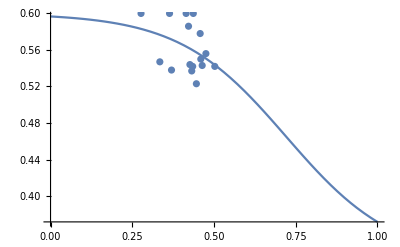

```mathematica
Module[{function=HydropCalcN[#](*i[#]*)(*,Abs[(StringCount[#,{"R","K"}]+StringCount[#,{"D","E"}])/StringLength[#]]*)&,datz,fitz},datz=Flatten[{Transpose[{function/@{NSP,N98,IBB,NUS,NLS,N49,NUL},{0.6,0.556,0.538,0.578,0.6,0.537,0.523}}],Transpose[{function/@{SEQPNt,SEQRNaseA,SEQFhuA(*,seqHisPdomain*)},{0.542,0.544,0.543(*,0.48*)}}],Transpose[{function/@{Ash1,AFP,MET2,ID3,Msh6,P1to60(*,PROTL*)},{0.6,0.55,0.542,0.586,0.547,0.6(*,0.58*)}}]},1];fitz=NonlinearModelFit[datz,0.33+(0.6-0.33)(1+Exp[b*x-c])^-1,{a,b,c},x,MaxIterations->100000];Print[Normal[fitz]];Show[Plot[fitz[x],{x,0,1}],ListPlot[datz]]]
```

```mathematica
{Mean[(0.333333333+(0.394)(1+Exp[20.46090067707921#-8.639176396733175])^-1)&/@#],Mean[(0.33+0.26999999999999996/(1+ⅇ^(-4.3935913152838815+6.094559463564209 #)))&/@#]}&@(HydropCalcN/@SeqsPDB)
(%-0.33)/(0.6-0.33)
```

{0.45712,0.552857}

{0.470816,0.825395}

```mathematica
(0.49-0.33)/(0.6-0.33)
```

0.592593

```mathematica
Mean[(HydropCalcN/@SeqsPDB)]
```

0.463847

#### Convert Lemke Data to νs as done in Hofmann

```mathematica
-Graphics-;
```

```mathematica
{N49νH,BBLνH,NLSνH,CSPνH,NUSνH,IBBνH,TRXνH,NULνH,N98νH,NSPνH}=NSolve[Sqrt[(2*0.4*0.38)/((2ν+1)(2ν+2))](#[[1]])^ν==Sqrt[6]^-1#[[2]],ν,Reals][[-1,1,2]]&/@Transpose[{{36,39,44,58,80,97,107,112,151,176},{3.6,0.0,4.3,0.0,6.2,6.4,0.0,6.6,5.3,6.9}}]
```

Part::partw: Part -1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{0.530618,{}⟦-1,1,2⟧,0.554508,{}⟦-1,1,2⟧,0.5641,0.543736,{}⟦-1,1,2⟧,0.531615,0.440995,0.48653}

#### Figures

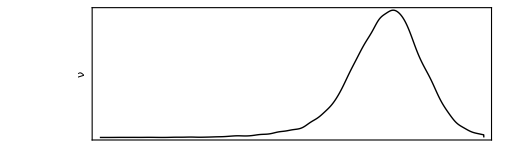

```mathematica
SmoothHistogram[HydropCalcN/@SeqsPDB
,PlotRange->{{0.24,0.54},(*{0.0,0.5},*){0,All}}
,ImageSize->{512,Automatic(*432*)}
,FrameTicks->None
,FrameTicksStyle->Directive[{Black,Thick}]
,PlotStyle->Directive[Thick,Black]
,ImagePadding->{{(*30*)150(*(150)*),(*150*)30(*(30)*)},{80,20}}
,PlotRangeClipping->True
,Frame->{{False,False},{True,False}}
,Axes->False
,AspectRatio->0.3
,FrameStyle->Thick
,BaseStyle->{Black,25,FontFamily->"Arial"}
,FrameLabel->{(*Style["Fractional Charge",Black,25,FontFamily->"Arial"]*)Style["",Black,25,FontFamily->"Arial"],Style["ν",Black,25,FontFamily->"Arial"]}]
```

```mathematica
Solve[0.333333333+(0.394)(1+Exp[20.46090067707921*x-8.639176396733175])^-1==0.5]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.4374}}

```mathematica
N[Length[Select[HydropCalcN/@SeqsPDB,#>0.4374&]]/Length[SeqsPDB]]
```

0.825727

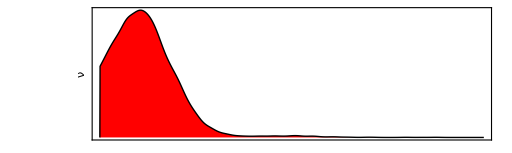

{512,200}

```mathematica
SmoothHistogram[HydropCalcN/@SeqsPDB
,PlotRange->{{0.4374,0.54+(0.4374-0.24)},(*{0.0,0.5},*){0,All}}
,ImageSize->{512,Automatic(*432*)}
,FrameTicks->None
,FrameTicksStyle->Directive[{Black,Thick}]
,PlotStyle->Directive[Thick,Black]
,ImagePadding->{{(*30*)150(*(150)*),(*150*)30(*(30)*)},{80,20}}
,PlotRangeClipping->True,FillingStyle->Red
,Frame->{{False,False},{True,False}}
,Axes->False
,AspectRatio->0.3,Filling->(Bottom)
,FrameStyle->Thick
,BaseStyle->{Black,25,FontFamily->"Arial"}
,FrameLabel->{(*Style["Fractional Charge",Black,25,FontFamily->"Arial"]*)Style["",Black,25,FontFamily->"Arial"],Style["ν",Black,25,FontFamily->"Arial"]}]
ImageDimensions[%]
```

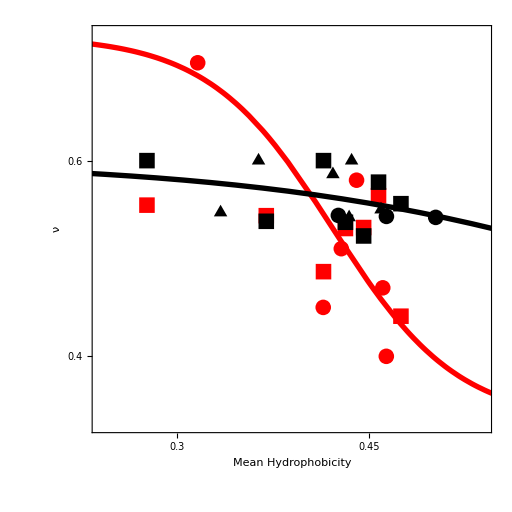

```mathematica
Module[{function=HydropCalcN[#](*i[#]*)(*,Abs[(StringCount[#,{"R","K"}]+StringCount[#,{"D","E"}])/StringLength[#]]*)&
,symbols={"■","■","■","●","●","▲","●","●","●"}
,words=Flatten[{"","","","","","","","","Expanded\n/Structured\nLine"}]
,sizesymbols=8*{2,2,2,2,2,2,2,2,2}
,colors=Flatten[{Orange,Red,Black,Red,Black,Black,Red,Red,Red}]},If[(Length[symbols]≠Length[words])||(Length[symbols]≠ Length[sizesymbols])||(Length[symbols]≠Length[colors]),Print[{Length[symbols],Length[words],Length[sizesymbols],Length[colors]}];Abort[]];Grid[{
{Show[ListPlot[{{0,0},Transpose[{function/@{NSP,N98,IBB,NUS,NLS,N49,NUL},{NSPνH,N98νH,IBBνH,NUSνH,NLSνH,N49νH,NULνH}}],Transpose[{function/@{NSP,N98,IBB,NUS,NLS,N49,NUL},{0.6,0.556,0.538,0.578,0.6,0.537,0.523}}],Transpose[{function/@{Csp,R15,R17,hCyp,IN,Prota},{0.47,0.45,0.51,0.40,0.58,0.7}}],Transpose[{function/@{SEQPNt,SEQRNaseA,SEQFhuA(*,seqHisPdomain*)},{0.542,0.544,0.543(*,0.48*)}}],Transpose[{function/@{Ash1,AFP,MET2,ID3,Msh6,P1to60(*,PROTL*)},{0.6,0.55,0.542,0.586,0.547,0.6(*,0.58*)}}]}
,PlotRange->{{0.24,0.54},(*{0.0,0.5},*){0.33,0.73}}
,PlotMarkers->Transpose[{symbols,sizesymbols}]
,ImageSize->512
,FrameTicks->{{Table[{0.1i ,PaddedForm[(0.1i ),{3,1}],{0,0.05}},{i,-6,11}],Table[{0.26999999999999996 (1.2222222222222223+i) ,Round[100i](*PaddedForm[N[100((0.1i-0.33)/(0.6-0.33) )],{3,1}]*),{0,0.05}},{i,0,1,0.2}]}
,{Table[{0.05i ,If[i==Round[i],PaddedForm[(0.05i ),{3,If[EvenQ[i],1,2]}],""],{0,0.05}},{i,-6,11}],None}}
,FrameTicksStyle->Directive[{Black,Thick}]
,PlotStyle->Table[{colors[[i]],"○",Thickness[0.01],Opacity[1]},{i,Length[symbols]}]
,ImagePadding->{{(*30*)150(*(150)*),(*150*)30(*(30)*)},{80,20}}
,PlotRangeClipping->True
,Frame->True
,Axes->False
,AspectRatio->1
,FrameStyle->Thick
,BaseStyle->{Black,25,FontFamily->"Arial"}
,FrameLabel->{(*Style["Fractional Charge",Black,25,FontFamily->"Arial"]*)Style["Mean Hydrophobicity",Black,25,FontFamily->"Arial"],Style["ν",Black,25,FontFamily->"Arial"]}],Plot[{0.333333333+(0.394)(1+Exp[20.46090067707921x-8.639176396733175])^-1,0.33+0.26999999999999996/(1+ⅇ^(-4.3935913152838815+6.094559463564209 x))},{x,0,1},Exclusions->None,PlotStyle->{Directive[Red,Thickness[0.0075],AbsoluteDashing[None]],Directive[Black,Thickness[0.0075],AbsoluteDashing[None]]}]]}}]]
```

## Fig. 2B

Data used in this figure are from. “Decoupling of size and shape fluctuations in heteropolymeric sequences reconciles discrepancies in SAXS vs. FRET measurements.” (Fuertes et al., 2016 PNAS).

Please contact the authors of that paper for access to their data.

```mathematica
NLSU=Module[{data,FUNC=FITGENERALi["PNt_ALLH_MP0p7"],fit},data=Select[{#[[1]]/10,#[[2]],#[[3]]}&/@Select[Import["/Users/josh/Downloads/SAXSdatasetPNAS2017/NLS/nlsupbs_merge.dat"],(Length[#]==3)&&NumberQ[#[[1]]]&],0.01≤#[[1]]≤0.15&];fit=NonlinearModelFit[data[[;;,;;2]],Evaluate[Abs[I0] FUNC[Abs[0.6],Abs[Rg] q]⟦1⟧],{{I0,data[[1,2]]},{ν,0.6},{Rg,24.25}},q,Weights->(1/(#1⟦3⟧)^2&)/@data,MaxIterations->Infinity];Print[Flatten[{fit["ANOVATable"][[1,1,3,4]],fit["BestFitParameters"][[{1,3,2},2]]}]];
fit=NonlinearModelFit[data[[;;,;;2]],Evaluate[Abs[I0] FUNC[Abs[ν],Abs[Rg] q]⟦1⟧],{{I0,fit["BestFitParameters"][[1,2]]},{ν,0.6},{Rg,fit["BestFitParameters"][[3,2]]}},q,
Weights->(1/(#1⟦3⟧)^2&)/@data,MaxIterations->100];
Flatten[{fit["ANOVATable"][[1,1,3,4]],fit["BestFitParameters"][[{1,3,2},2]]}]]
```

{0.59375,178.501,24.2253,0.6}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.592761,178.491,24.2268,0.602811}

```mathematica
NLSL=Module[{data,FUNC=FITGENERALi["PNt_ALLH_MP0p7"],fit},data=Select[{#[[1]]/10,#[[2]],#[[3]]}&/@Select[Import["/Users/josh/Downloads/SAXSdatasetPNAS2017/NLS/nlslpbs_merge.dat"],(Length[#]==3)&&NumberQ[#[[1]]]&],0.01≤#[[1]]≤0.15&];fit=NonlinearModelFit[data[[;;,;;2]],Evaluate[Abs[I0] FUNC[Abs[0.6],Abs[Rg] q]⟦1⟧],{{I0,data[[1,2]]},{ν,0.6},{Rg,23.03}},q,Weights->(1/(#1⟦3⟧)^2&)/@data,MaxIterations->Infinity];Print[Flatten[{fit["ANOVATable"][[1,1,3,4]],fit["BestFitParameters"][[{1,3,2},2]]}]];
fit=NonlinearModelFit[data[[;;,;;2]],Evaluate[Abs[I0] FUNC[Abs[ν],Abs[Rg] q]⟦1⟧],{{I0,fit["BestFitParameters"][[1,2]]},{ν,0.6},{Rg,fit["BestFitParameters"][[3,2]]}},q,Weights->(1/(#1⟦3⟧)^2&)/@data,MaxIterations->100];
Flatten[{fit["ANOVATable"][[1,1,3,4]],fit["BestFitParameters"][[{1,3,2},2]]}]]
```

{0.815019,235.721,23.52,0.6}

{0.776514,232.154,23.0422,0.518129}

```mathematica
COLORS2={Black,Red};
```

```mathematica
ErrorListPlot[{{{NLSU[[3]]Mean[#[[;;,1]]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/Sqrt[Length[#[[;;,2]]]]]}&/@Split[{(#[[1]])/10,(NLSU[[3]](#[[1]])/10)^2(#[[2]])/NLSU[[2]],(NLSU[[3]](#[[1]])/10)^2(#[[3]])/NLSU[[2]]}&/@Select[Import["/Users/josh/Downloads/SAXSdatasetPNAS2017/NLS/nlsupbs_merge.dat"],(Length[#]==3)&&NumberQ[#[[1]]]&],Round[15Log10[#1⟦1⟧]]==Round[15 Log10[#2⟦1⟧]]&],{{NLSU[[3]]Mean[#[[;;,1]]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/Sqrt[Length[#[[;;,2]]]]]}&/@Split[{(#[[1]])/10,(NLSL[[3]](#[[1]])/10)^2(#[[2]])/NLSL[[2]],(NLSL[[3]](#[[1]])/10)^2(#[[3]])/NLSL[[2]]}&/@Select[Import["/Users/josh/Downloads/SAXSdatasetPNAS2017/NLS/nlslpbs_merge.dat"],(Length[#]==3)&&NumberQ[#[[1]]]&],Round[15Log10[#1⟦1⟧]]==Round[15 Log10[#2⟦1⟧]]&]},PlotRange->{{0,10},{0,3}},Prolog->Flatten[Table[{COLORS2[[j]],Thickness[0.0075],JoinedCurve[BezierCurve[Table[{x,x^2 FITGENERALi["PNt_ALLH_MP0p7"][{NLSU[[4]],NLSL[[4]]}[[j]],x][[1]]},{x,0.01,0.15{NLSU[[3]],NLSL[[3]]}[[j]],.05}]]],AbsoluteDashing[{2,13}],JoinedCurve[BezierCurve[Table[{x,x^2 FITGENERALi["PNt_ALLH_MP0p7"][{NLSU[[4]],NLSL[[4]]}[[j]],x][[1]]},{x,0.15{NLSU[[3]],NLSL[[3]]}[[j]],13.,.05}]]],AbsoluteDashing[None]},{j,2}]],ImageSize->512,FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(120),(15)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotStyle->Table[{COLORS2[[i]],"●",Thickness[0.01]},{i,2}]
,AspectRatio->1
,ErrorBarFunction->Function[{coords, errs},{Thickness[0.005],AbsolutePointSize[6],Point[coords],Line[{coords+{0.006,errs[[2,1]]},coords+{0.006,errs[[2,2]]}}]}]
(*,PlotMarkers->{"●",10}*)
,FrameStyle->Thick
,Axes->False
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style[(*"qR_g"*)"",Black,25,FontFamily->"Arial"],Style[(*"(qR_g)^2I(q)/I_0"*)"",Black,25,FontFamily->"Arial"]},FrameTicks->Module[{plotrange={{0,5*5(*5*6*)},{0,5*1(*2.5*)}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]],If[Round[i]==i,Round[Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]]](*PaddedForm[f2[(Round[(plotrange[[2,2]]-plotrange[[2,1]])/5,10^(-paddedform[[2,2]])]i +plotrange[[2,1]])//N],If[Length[#]==4,#[[3;;]],#]&@paddedform[[2]]]*),""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,0.25}],None}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[i]==i,Round[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]]](*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,0.2}],None}}]]
```

StandardDeviation::shlen: The argument {-0.174261} should have at least two elements.

StandardDeviation::shlen: The argument {-0.0149908} should have at least two elements.

StandardDeviation::shlen: The argument {0.0475605} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

-Graphics-

## Fig. 2C

Data used in this figure are from “Random coil negative control reproduces the discrepancy between scattering and FRET measurements of denatured protein dimensions.” (Watkins et al., 2015 PNAS).

```mathematica
Data5KdaUrea={{2,23.06,0.23},{4,22.86,0.23},{8,23.2,0.26}};
```

```mathematica
Data5KdaGdn={{2,21.94,0.46},{4,23.49,0.21},{6,22.78,0.25},{8,22.02,0.23},{0,22.58,0.26}};
```

```mathematica
NonlinearModelFit[Data5KdaGdn[[;;,;;2]],a+0 x,{a,b},x,Weights->(#^-2&/@Data5KdaGdn[[;;,3]])]
Normal[%]
```

FittedModel[22.7126]

22.7126

```mathematica
Esaw=Interpolation[Table[{x,NIntegrate[(3.7573448136933925 ⅇ^(-1.269 ( ρ)^2.427) (ρ)^2.269)/(1+x^6 ρ^6),{ρ,0,3}]},{x,0.1,3.,0.05}]];
```

PEG data Gdn

```mathematica
datapnts={{385.2121913580246,730.8574459876543},{466.5451388888888,751.9068287037036},{548.3979552469134,730.5285493827159},{629.5081018518517,706.2326388888888},{710.3317901234566,690.4456018518517},{873.1462191358022,659.7627314814814},{954.5852623456786,642.8935185185185},{1034.6768904320984,630.2363040123456},{1115.9992283950614,616.9955632716049},{1192.7276234567898,605.0704089506172},{1270.0077160493825,590.270061728395},{1354.7357253086416,578.1857638888888}};
```

```mathematica
yvals={{389.43479938271594,371.5219907407409},{388.29957561728395,628.3265817901236}};
```

```mathematica
xvals={{386.0397376543209,117.26369598765473},{711.0214120370367,119.52353395061732}};
```

```mathematica
changecords[a_]:=Module[{tmp=Sort[xvals[[;;,1]]],tmp2=Sort[yvals[[;;,2]]]},{2(a[[1]]-tmp[[1]])/(tmp[[2]]-tmp[[1]]),0.2(a[[2]]-tmp2[[1]])/(tmp2[[2]]-tmp2[[1]])+0.2}]
```

```mathematica
changedata=changecords/@datapnts;
```

```mathematica
LinearModelFit[{#[[1]],x/.FindMinimum[(#[[2]]-Esaw[x])^2,{x,1}][[2]]}&/@changedata,{x,x^2},x]
%[8]
```

FittedModel[1.11867+0.0307621 x+0.000898154 x^2]

1.42225

Peg data Urea

```mathematica
datapnts={{742.4281813865147,315.7179487179488},{707.1325973409306,321.7771248812916},{672.1498100664767,321.09099002849007},{636.8895417853751,323.90111585944925},{600.8523266856599,326.72637701804376},{567.6857787274454,334.0115147198481},{531.8957739791073,331.77148622981963},{496.1663105413105,341.5186372269706},{461.4610042735043,341.2714268755936},{426.2663224121557,345.110754985755},{390.8092948717948,348.5464743589744},{355.78110161443493,353.26869658119665},{320.03650284900283,358.22299382716056},{284.5441595441595,364.65550807217477},{250.70156695156692,372.21308167141507},{214.08416429249758,379.11983618233626},{180.0195868945869,389.8205128205129}};
```

```mathematica
xvals={{320.4956077872744,111.51210826210843},{180.4534662867996,111.4162511870847}};
```

```mathematica
yvals={{176.50819088319088,340.8425925925927},{176.08944681861345,228.260980531814}};
```

```mathematica
changedata2=changecords/@datapnts;
```

```mathematica
NonlinearModelFit[{#[[1]],x/.FindMinimum[(#[[2]]-Esaw[x])^2,{x,1}][[2]]}&/@changedata2[[;;]],Ree0+(a*x)/(k^2+x),{Ree0,a,k},x,Method->"LevenbergMarquardt",MaxIterations->Infinity]
%[16]
```

FittedModel[1.13395+(0.46806 x)/(10.7376+x)]

1.41404

Figure

```mathematica
ErrorListPlot[{({{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&/@Data5KdaGdn),{{#[[1]],(x/.FindMinimum[(#[[2]]-Esaw[x])^2,{x,1}][[2]])/(1.3919242979155793/22.71261456740454)},ErrorBar[0]}&/@changedata,({{0.5#[[1]],#[[2]]},ErrorBar[#[[3]]]}&/@Data5KdaUrea),{{0.5#[[1]],(x/.FindMinimum[(#[[2]]-Esaw[x])^2,{x,1}][[2]])/(1.4140399327578406/22.71261456740454)},ErrorBar[0]}&/@changedata2},PlotRange->{{-0.1,8.15},{17.5,24.5}},Prolog->{Black,Thickness[0.0075],(*JoinedCurve[BezierCurve[Table[{x,(0.5233716747115598+0.6437105102302414 x)/(1+1.0267969740270213 x)},{x,-1,20,.05}]]]*)JoinedCurve[BezierCurve[Table[{x,22.71261456740454},{x,0.,20,.05}]]],Red,JoinedCurve[BezierCurve[Table[{x,22.71261456740454*((1.0955973311871632+(1.4569200209673985 x)/(31.332769124658636+x))/1.3919242979155793)},{x,0.,20,.05}]]],JoinedCurve[BezierCurve[Table[{0.5x,22.71261456740454*((1.1339487362837217+(0.4680603456371334 x)/(10.737596984366952+x))/1.4140399327578406)},{x,0.,20,.05}]]],Gray,AbsoluteDashing[10],(*JoinedCurve[BezierCurve[Table[{x,-0.6763319396675016fitνandRg[FITname][0.5388661788322268+(0.07299289622722452 (x))/(0.9764990304057557+(x))](108/334)^(0.5388661788322268+(0.07299289622722452 (x))/(0.9764990304057557+(x)))},{x,0,20,.05}]]],*)Thickness[0.01],AbsoluteDashing[10],Gray,Darker[Green],Gray(*,AbsoluteDashing[0],Red*),Black},ImageSize->{Automatic,477(*512/889*)},FrameTicksStyle->Directive[{Black,Thick}]
,ImagePadding->{{(125),125(*(10+40)*)},{90,10}}
,PlotRangeClipping->True
,Frame->True
,Joined->False
,PlotMarkers->(If[#==0,{"■",20},{"●",15}]&/@{1,1,0,0})
,PlotStyle->(If[#==0,Black,Red]&/@{0,1,0,1})
,AspectRatio->1(*0.6*)(*0.5*)
,ErrorBarFunction->Function[{coords, errs}, {Thickness[2*0.01/3],Line[{coords+{-0.0065,errs[[2,1]]},coords+{-0.0065,errs[[2,2]]}}]}]
,FrameStyle->Thick
,Axes->False
,BaseStyle->{25,FontFamily->"Arial"}
,FrameLabel->{Style[(*"[Gdn] (M)"*)"",Black,25,FontFamily->"Arial"],Rotate[Style[(*"R_g\n(Å)"*)"",Black,25,FontFamily->"Arial"],-Pi/2]},FrameTicks->Module[{plotrange={{0,0.5*1.25*8},{0,0.25*5*10}},paddedform={{2,1},{3,1}},f1=#&,f2=#&},{{Table[{Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]],If[Round[i]==i,Round[Round[(plotrange[[2,2]]-plotrange[[2,1]])/5(*10^(-paddedform[[2,2]])*)]i+plotrange[[2,1]]](*PaddedForm[f2[(Round[(plotrange[[2,2]]-plotrange[[2,1]])/5,10^(-paddedform[[2,2]])]i +plotrange[[2,1]])//N],If[Length[#]==4,#[[3;;]],#]&@paddedform[[2]]]*),""],{0,If[Round[i]==i,0.05,0.025]}},{i,-2,25,0.2}],Table[{22.71261456740454*0.1i,If[Round[i]==i,PaddedForm[0.1i,{2,1}],""],{0,If[Round[i]==i,0.05,0.025]}},{i,0,10,0.2}]}
,{Table[{Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]],If[Round[i]==i,Round[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,0.1(*10^(-paddedform[[1,2]])*)]i+plotrange[[1,1]]](*PaddedForm[f1[Round[(plotrange[[1,2]]-plotrange[[1,1]])/5,10^(-paddedform[[1,2]])]i+plotrange[[1,1]]]//N,paddedform[[1]]]*),""],{0,If[Round[i]==i,1,0.5]*0.035}},{i,-2,25,0.5}],None}}]]
```

-Graphics-